```mathematica
vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};
```

```mathematica
eq1=A0[1]==0
eq2=-q1/(2 k1) y1^2+A0[1] y1+B0[1]==-q2/(2 k2) y1^2+A0[2] y1+B0[2]
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]
.18.03
```

```mathematica
здесь начали решать и вводить уравнения
```

A0[1]==0

-(q1 y1^2)/(2 k1)+y1 A0[1]+B0[1]==-(q2 y1^2)/(2 k2)+y1 A0[2]+B0[2]

-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]

.03 .18

```mathematica
eq1=A0[1]==0
```

A0[1]==0

```mathematica
eq2=-q1/(2 k1) y1^2+A0[1] y1+B0[1]==-q2/(2 k2) y1^2+A0[2] y1+B0[2]
```

-(q1 y1^2)/(2 k1)+y1 A0[1]+B0[1]==-(q2 y1^2)/(2 k2)+y1 A0[2]+B0[2]

```mathematica
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]
```

-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2]

```mathematica
eq4=-q2/(2 k2) y2^2+A0[2] y2+B0[2]==-q3/(2 k3) y2^2+A0[3] y2+B0[3]
```

-(q2 y2^2)/(2 k2)+y2 A0[2]+B0[2]==-(q3 y2^2)/(2 k3)+y2 A0[3]+B0[3]

```mathematica
eq5 = -q2 y2 + k2 A0[2] == -q3 y2 + k3 A0[3]
```

```mathematica
eq6 =-q3/(2k3)y3^2+A0[3]y3+B0[3]==-q4/(2k4)y3^2+A0[4]y3+B0[4]
```

-(q3 y3^2)/(2 k3)+y3 A0[3]+B0[3]==-(q4 y3^2)/(2 k4)+y3 A0[4]+B0[4]

```mathematica
eq7=-q3y3+k3A0[3]==-q4y3+k4A0[4]
```

-q3y3+k3A0[3]==-q4y3+k4A0[4]

```mathematica
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5]
```

-(q4 y4^2)/(2 k4)+y4 A0[4]+B0[4]==-(q5 y4^2)/(2 k5)+y4 A0[5]+B0[5]

```mathematica
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5]
```

-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5]

```mathematica
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6]
```

-(q5 y5^2)/(2 k5)+y5 A0[5]+B0[5]==-(q6 y5^2)/(2 k6)+y5 A0[6]+B0[6]

```mathematica
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6]
```

-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6]

```mathematica
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7]
```

-(q6 y6^2)/(2 k6)+y6 A0[6]+B0[6]==-(q7 y6^2)/(2 k7)+y6 A0[7]+B0[7]

```mathematica
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7]
```

-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7]

```mathematica
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8]
```

-(q7 y7^2)/(2 k7)+y7 A0[7]+B0[7]==-(q8 y7^2)/(2 k8)+y7 A0[8]+B0[8]

```mathematica
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8]
```

```mathematica
-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8]
```

```mathematica
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9]
```

-(q8 y8^2)/(2 k8)+y8 A0[8]+B0[8]==-(q9 y8^2)/(2 k9)+y8 A0[9]+B0[9]

```mathematica
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9]
```

-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9]

```mathematica
eq18 = -(q9/k9)*y9+A0[9]== -(2*qr/w)*(b-a);
```

```mathematica
system={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};
```

```mathematica
vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};
```

```mathematica
solution=Solve[system,vars]
```

Solve::naqs: «1» is not a quantified system of equations and inequalities.

Solve[{A0[1]==0,-(q1 y1^2)/(2 k1)+y1 A0[1]+B0[1]==-(q2 y1^2)/(2 k2)+y1 A0[2]+B0[2],-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2],-(q2 y2^2)/(2 k2)+y2 A0[2]+B0[2]==-(q3 y2^2)/(2 k3)+y2 A0[3]+B0[3],eq5,-(q3 y3^2)/(2 k3)+y3 A0[3]+B0[3]==-(q4 y3^2)/(2 k4)+y3 A0[4]+B0[4],-q3y3+k3A0[3]==-q4y3+k4A0[4],-(q4 y4^2)/(2 k4)+y4 A0[4]+B0[4]==-(q5 y4^2)/(2 k5)+y4 A0[5]+B0[5],-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5],-(q5 y5^2)/(2 k5)+y5 A0[5]+B0[5]==-(q6 y5^2)/(2 k6)+y5 A0[6]+B0[6],-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6],-(q6 y6^2)/(2 k6)+y6 A0[6]+B0[6]==-(q7 y6^2)/(2 k7)+y6 A0[7]+B0[7],-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7],-(q7 y7^2)/(2 k7)+y7 A0[7]+B0[7]==-(q8 y7^2)/(2 k8)+y7 A0[8]+B0[8],-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8],-(q8 y8^2)/(2 k8)+y8 A0[8]+B0[8]==-(q9 y8^2)/(2 k9)+y8 A0[9]+B0[9],-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9],-(q9 y9)/k9+A0[9]==-(2 (-a+b) qr)/w},{A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]}]

```mathematica
(*Все переменные*)vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижняя граница*)
eq1=A0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхняя граница*)
f0=-2 qr (b-a)/w;
eq18=-(q9/k9) y9+A0[9]==f0;

(*Собираем систему*)
system={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(*Пытаемся решить символьно*)
solution=Solve[system,vars]
```

{}

```mathematica
solution=Solve[system,vars]
```

{}

```mathematica
params={q1->0.1,k1->0.5,y1->0.2,q2->0.15,k2->0.6,y2->0.4,q3->0.12,k3->0.55,y3->0.6,q4->0.13,k4->0.58,y4->0.8,q5->0.14,k5->0.6,y5->1.0,q6->0.11,k6->0.52,y6->1.2,q7->0.1,k7->0.5,y7->1.4,q8->0.09,k8->0.48,y8->1.6,q9->0.08,k9->0.45,y9->1.8,qr->1.0,w->2.0,a->0.8,b->1.2};
```

```mathematica
solutionNum=Solve[system/.params,vars]
```

{}

```mathematica
(*Два слоя,неизвестные:A0[1],B0[1],A0[2],B0[2]*)vars2={A0[1],B0[1],A0[2],B0[2]};

(*Нижняя граница*)
eq1=A0[1]==0;

(*Стык 1-2*)
eq2=-q1/(2 k1) y1^2+A0[1] y1+B0[1]==-q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Верхняя граница:поток задан*)
f0=-2 qr (b-a)/w;
eq4=-(q2/k2) y2+A0[2]==f0;

system2={eq1,eq2,eq3,eq4};

(*Численные параметры*)
params={q1->1,k1->1,y1->1,q2->2,k2->2,y2->2,qr->1,w->10,a->3,b->7};

Solve[system2/.params,vars2]
```

{}

```mathematica
Solve[{x+y==2,x-y==0},{x,y}]
```

{{x→1,y→1}}

```mathematica
vars={A1,B1,A2,B2};

eq1=A1==0;
eq2=-q1/(2 k1) y1^2+A1 y1+B1==-q2/(2 k2) y1^2+A2 y1+B2;
eq3=-q1 y1+k1 A1==-q2 y1+k2 A2;
eq4=-q2/k2 y2+A2==f0;

system={eq1,eq2,eq3,eq4};

params={q1->1,k1->1,y1->1,q2->2,k2->2,y2->2,f0->5};

Solve[system/.params,vars]
```

{}

```mathematica
vars={A1,B1,A2,B2};

eq1=A1==0;
eq2=-q1/(2 k1) y1^2+A1 y1+B1==-q2/(2 k2) y1^2+A2 y1+B2;
eq3=-q1 y1+k1 A1==-q2 y1+k2 A2;
eq4=-q2/k2 y2+A2==f0;

system={eq1,eq2,eq3,eq4};

params={q1->1,k1->1,y1->1,q2->2,k2->2,y2->2,f0->-1.5};

Solve[system/.params,vars]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{A1→0.,A2→0.5,B2→-0.5+1. B1}}

```mathematica
Reduce[system/.params, vars]
```

False

```mathematica
vars={A1,B1,A2,B2};

eq1=A1==0;
eq2=-q1/(2 k1) y1^2+A1 y1+B1==-q2/(2 k2) y1^2+A2 y1+B2;
eq3=-q1 y1+k1 A1==-q2 y1+k2 A2;
eq4=-q2/k2 y2+A2==f0;
eq5=B1==0;(* <-новая*)system={eq1,eq2,eq3,eq4,eq5};

params={q1->1,k1->1,y1->1,q2->2,k2->2,y2->2,f0->-1.5};

Solve[system/.params,vars]
```

{{A1→0.,B1→0.,A2→0.5,B2→-0.5}}

```mathematica
(*Все неизвестные*)vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижняя граница:теплоизоляция*)
eq1=A0[1]==0;

(*Фиксация калибровки:температура в начале координат*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхняя граница:поток от провода (средняя составляющая)*)
f0=-2 qr (b-a)/w;
eq18=-(q9/k9) y9+A0[9]==f0;

(*Собираем всё вместе*)
system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(*Проверяем количество уравнений*)
Length[system]  (*должно быть 19*)
Length[vars]    (*должно быть 18*)

(*Решаем*)
solution=Solve[system/.params,vars]
```

19

18

{}

```mathematica
(*Все неизвестные*)vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижняя граница:теплоизоляция*)
eq1=A0[1]==0;

(*Фиксация калибровки:температура в начале координат*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхняя граница:поток от провода (средняя составляющая)*)
f0=-2 qr (b-a)/w;
eq18=-(q9/k9) y9+A0[9]==f0;

(*Собираем всё вместе*)
system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(*Проверяем количество уравнений*)
Length[system]  (*должно быть 19*)
Length[vars]    (*должно быть 18*)

(*Решаем*)
solution=Reduce[system/.params,vars]
```

19

18

$Aborted

```mathematica
(* =====ЧИСЛЕННЫЕ ПАРАМЕТРЫ=====*)(*Вставьте сюда свои значения*)(*Геометрия*)y1=0.2;(*толщина слоя 1*)y2=0.4;(*и т.д.до y9*)y3=0.6;
y4=0.8;
y5=1.0;
y6=1.2;
y7=1.4;
y8=1.6;
y9=1.8;

(*Теплопроводности*)
k1=0.5;k2=0.6;k3=0.55;k4=0.58;k5=0.6;
k6=0.52;k7=0.5;k8=0.48;k9=0.45;

(*Источники тепла (q_i)*)
q1=0.1;q2=0.15;q3=0.12;q4=0.13;q5=0.14;
q6=0.11;q7=0.1;q8=0.09;q9=0.08;

(*Параметры провода*)
qr=1.0;(*плотность потока на проводе*)w=2.0;(*ширина структуры*)a=0.8;(*начало контакта*)b=1.2;(*конец контакта*)(* =====СИСТЕМА УРАВНЕНИЙ=====*)vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

eq1=A0[1]==0;
eqFix=B0[1]==0;(*фиксация калибровки*)eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

f0=-2 qr (b-a)/w;
eq18=-(q9/k9) y9+A0[9]==f0;

(* =====РЕШЕНИЕ=====*)

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

solution=NSolve[system,vars]   (*NSolve для численного решения*)
```

{}

```mathematica
(*Численные параметры*)y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

w=100*10^-6;a=25*10^-6;b=75*10^-6;qr=7.92*10^7;
f0=2 qr (b-a)/w;(* =====ЧИСЛЕННЫЕ ПАРАМЕТРЫ=====*)(*Вставьте сюда свои значения*)(*Геометрия*)y1=0.2;(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (в метрах)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0=-2 qr (b-a)/w;

(*Источники тепла (пока оценочно)*)
q1=1*10^12;
q2=1*10^12;
q3=1*10^12;
q4=1*10^12;
q5=1*10^12;
q6=1*10^12;
q7=1*10^12;
q8=1*10^12;
q9=1*10^12;(* =====СИСТЕМА УРАВНЕНИЙ=====*)vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

eq1=A0[1]==0;
eqFix=B0[1]==0;(*фиксация калибровки*)eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

f0=-2 qr (b-a)/w;
eq18=-(q9/k9) y9+A0[9]==f0;

(* =====РЕШЕНИЕ=====*)

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

solution=Reduce[system,vars]   (*NSolve для численного решения*)(*положительный поток внутрь*)(*Упрощённые источники:только активный слой греется*)q1=0;q2=0;q3=0;q4=0;
q5=f0/y5;(*y5 здесь толщина активного слоя,но осторожно:y5-это координата,а не толщина!*)(*Правильно:толщина активного слоя d5=y5-y4=42e-9*)d5=42*10^-9;
q5=f0/d5;
q6=0;q7=0;q8=0;q9=0;

(*Далее система уравнений как у вас,но с правильным f0*)
vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

eq1=A0[1]==0;
eqFix=B0[1]==0;
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];
eq18=-(q9/k9) y9+A0[9]==f0;

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

solution=Reduce[system,vars]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},«17»,{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.90948×10^7}} may contain significant numerical errors.

Set::write: Tag Times in 1000000000000 False is Protected.

False

```mathematica
(* ===ПАРАМЕТРЫ===*)y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

w=100*10^-6;a=25*10^-6;b=75*10^-6;qr=7.92*10^7;
f0target=2 qr (b-a)/w;(*целевой средний поток*)(*Источники:только активный слой (i=5)*)q1=0;q2=0;q3=0;q4=0;d5=42*10^-9;
q5=f0target/d5;(*предварительная оценка,потом уточним*)q6=0;q7=0;q8=0;q9=0;

(*Переменные*)
vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Уравнения без верхнего условия (eq18)*)
eq1=A0[1]==0;
eqFix=B0[1]==0;
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17};

sol=NSolve[system,vars]
```

{{A0[1]→2.42571×10^-8,B0[1]→0.,A0[2]→6.93435×10^-9,B0[2]→7.15301×10^-15,A0[3]→2.42571×10^-8,B0[3]→3.14222×10^-15,A0[4]→6.93435×10^-9,B0[4]→-1.16663×10^-13,A0[5]→7.29143×10^8,B0[5]→-845.806,A0[6]→-1.72174×10^6,B0[6]→3.78955,A0[7]→-6.02281×10^6,B0[7]→16.7444,A0[8]→-6.02281×10^6,B0[8]→16.7444,A0[9]→-2.26286×10^6,B0[9]→3.53942}}

```mathematica
(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (координаты границ слоёв,м)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода (только для справки,в системе не участвуют)*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0target=2 qr (b-a)/w;(*целевой средний поток,Вт/м.b2*)(*Источники тепла q_i (Вт/м.b3)—теперь все включены*)(*Для первого теста берём оценочные значения,позже заменим на реальные из сопротивлений*)q1=1*10^12;
q2=1*10^12;
q3=1*10^12;
q4=1*10^12;
q5=1*10^12;
q6=1*10^12;
q7=1*10^12;
q8=1*10^12;
q9=1*10^12;

(* ===СИСТЕМА УРАВНЕНИЙ (18 уравнений)===*)

vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижняя граница*)
eq1=A0[1]==0;
eqFix=B0[1]==0;(*фиксация калибровки*)(*Стык 1-2*)eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхнее условие (eq18) временно убрано*)

system={eq1,eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17};

(* ===РЕШЕНИЕ===*)

solution=NSolve[system,vars]
```

{{A0[1]→0.,B0[1]→0.,A0[2]→0.,B0[2]→-0.0391007,A0[3]→0.,B0[3]→0.0156511,A0[4]→0.,B0[4]→-0.0600766,A0[5]→0.,B0[5]→0.329952,A0[6]→0.,B0[6]→-0.0743261,A0[7]→0.,B0[7]→0.172012,A0[8]→0.,B0[8]→0.172012,A0[9]→0.,B0[9]→-0.120765}}

```mathematica
(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (координаты границ слоёв,м)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0=qr (b-a)/w;(*средний поток,положительный*)(*Источники тепла q_i (Вт/м.b3)—пока оценочные*)q1=1*10^12;
q2=1*10^12;
q3=1*10^12;
q4=1*10^12;
q5=1*10^12;
q6=1*10^12;
q7=1*10^12;
q8=1*10^12;
q9=1*10^12;

(* ===СИСТЕМА УРАВНЕНИЙ (17 уравнений)===*)

vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Калибровка:фиксируем аддитивную константу*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхнее условие (провод)*)
eq18=-(q9/k9) y9+A0[9]==f0;

system={eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(* ===РЕШЕНИЕ===*)

solution=NSolve[system,vars]
```

{{A0[1]→1.05679×10^8,B0[1]→0.,A0[2]→3.02105×10^7,B0[2]→90.5234,A0[3]→1.05679×10^8,B0[3]→-16.5875,A0[4]→3.02105×10^7,B0[4]→109.37,A0[5]→2.31614×10^8,B0[5]→-357.496,A0[6]→3.02105×10^7,B0[6]→117.814,A0[7]→1.05679×10^8,B0[7]→-109.251,A0[8]→1.05679×10^8,B0[8]→-109.251,A0[9]→3.97052×10^7,B0[9]→122.157}}

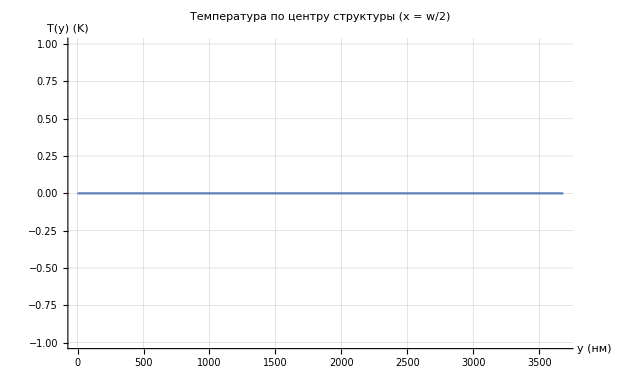

```mathematica
(*Извлекаем решение*)sol=solution[[1]];(*если решение выдано как список подстановок*)(*Определяем функцию температуры для каждого слоя*)T1[x_,y_]=-q1/(2 k1) y^2+(A0[1]/.sol) y+(B0[1]/.sol);
T2[x_,y_]=-q2/(2 k2) y^2+(A0[2]/.sol) y+(B0[2]/.sol);
T3[x_,y_]=-q3/(2 k3) y^2+(A0[3]/.sol) y+(B0[3]/.sol);
T4[x_,y_]=-q4/(2 k4) y^2+(A0[4]/.sol) y+(B0[4]/.sol);
T5[x_,y_]=-q5/(2 k5) y^2+(A0[5]/.sol) y+(B0[5]/.sol);
T6[x_,y_]=-q6/(2 k6) y^2+(A0[6]/.sol) y+(B0[6]/.sol);
T7[x_,y_]=-q7/(2 k7) y^2+(A0[7]/.sol) y+(B0[7]/.sol);
T8[x_,y_]=-q8/(2 k8) y^2+(A0[8]/.sol) y+(B0[8]/.sol);
T9[x_,y_]=-q9/(2 k9) y^2+(A0[9]/.sol) y+(B0[9]/.sol);

(*Собираем кусочно-определённую функцию по всей толщине*)
Ttotal[x_,y_]:=Piecewise[{{T1[x,y],0≤y≤y1},{T2[x,y],y1<y≤y2},{T3[x,y],y2<y≤y3},{T4[x,y],y3<y≤y4},{T5[x,y],y4<y≤y5},{T6[x,y],y5<y≤y6},{T7[x,y],y6<y≤y7},{T8[x,y],y7<y≤y8},{T9[x,y],y8<y≤y9}}]

(*Пример:профиль температуры по центру (x=w/2)*)
Plot[Ttotal[w/2,y*10^9],{y,0,y9*10^9},AxesLabel->{"y (нм)","T(y) (K)"},PlotLabel->"Температура по центру структуры (x = w/2)",GridLines->Automatic,PlotRange->All]
```

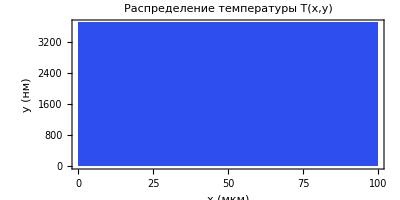

```mathematica
DensityPlot[Ttotal[x*10^6,y*10^9],{x,0,w*10^6},{y,0,y9*10^9},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"x (мкм)","y (нм)"},PlotLabel->"Распределение температуры T(x,y)",AspectRatio->0.5]
```

{A0[1]→1.07378×10^8,B0[1]→0.,A0[2]→3.09309×10^7,B0[2]→91.8383,A0[3]→1.08199×10^8,B0[3]→-17.3353,A0[4]→3.09309×10^7,B0[4]→110.946,A0[5]→2.37137×10^8,B0[5]→-363.552,A0[6]→3.09309×10^7,B0[6]→119.464,A0[7]→1.08199×10^8,B0[7]→-110.805,A0[8]→1.08199×10^8,B0[8]→-110.805,A0[9]→4.0652×10^7,B0[9]→123.493}

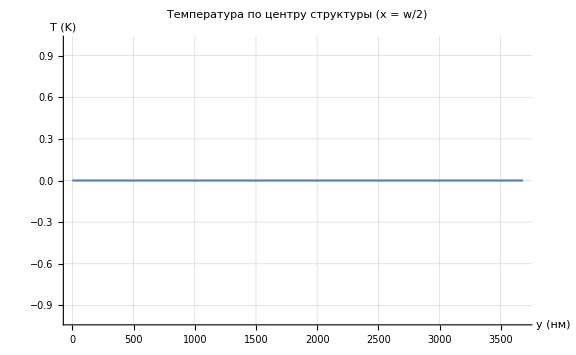

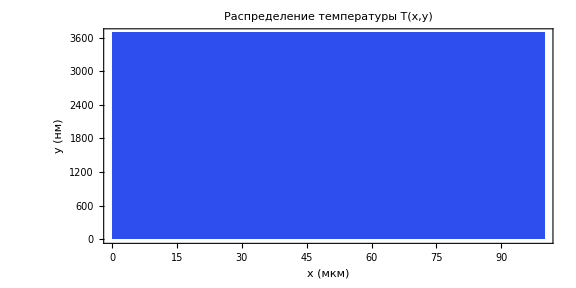

```mathematica
(* ===ЧИСЛЕННЫЕ ПАРАМЕТРЫ===*)(*Геометрия (координаты границ слоёв,м)*)y1=1200*10^-9;
y2=1420*10^-9;
y3=1670*10^-9;
y4=2320*10^-9;
y5=2362*10^-9;
y6=3012*10^-9;
y7=3162*10^-9;
y8=3512*10^-9;
y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=13.15;k2=46;k3=13.15;k4=46;k5=6;
k6=46;k7=13.15;k8=13.15;k9=35;

(*Параметры провода*)
w=100*10^-6;
a=25*10^-6;
b=75*10^-6;
qr=7.92*10^7;
f0=qr (b-a)/w;(*средний поток,положительный*)(*Источники тепла q_i (Вт/м.b3)—пока оценочные*)

q1=1*10^12;
q2=1*10^13;
q3=1*10^13;
q4=1*10^13;
q5=1*10^13;
q6=1*10^13;
q7=1*10^13;
q8=1*10^13;
q9=1*10^13;

(* ===СИСТЕМА УРАВНЕНИЙ (18×18)===*)

vars={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Калибровка:фиксируем аддитивную константу*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=-(q1/(2 k1)) y1^2+A0[1] y1+B0[1]==-(q2/(2 k2)) y1^2+A0[2] y1+B0[2];
eq3=-q1 y1+k1 A0[1]==-q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=-(q2/(2 k2)) y2^2+A0[2] y2+B0[2]==-(q3/(2 k3)) y2^2+A0[3] y2+B0[3];
eq5=-q2 y2+k2 A0[2]==-q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=-(q3/(2 k3)) y3^2+A0[3] y3+B0[3]==-(q4/(2 k4)) y3^2+A0[4] y3+B0[4];
eq7=-q3 y3+k3 A0[3]==-q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=-(q4/(2 k4)) y4^2+A0[4] y4+B0[4]==-(q5/(2 k5)) y4^2+A0[5] y4+B0[5];
eq9=-q4 y4+k4 A0[4]==-q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=-(q5/(2 k5)) y5^2+A0[5] y5+B0[5]==-(q6/(2 k6)) y5^2+A0[6] y5+B0[6];
eq11=-q5 y5+k5 A0[5]==-q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=-(q6/(2 k6)) y6^2+A0[6] y6+B0[6]==-(q7/(2 k7)) y6^2+A0[7] y6+B0[7];
eq13=-q6 y6+k6 A0[6]==-q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=-(q7/(2 k7)) y7^2+A0[7] y7+B0[7]==-(q8/(2 k8)) y7^2+A0[8] y7+B0[8];
eq15=-q7 y7+k7 A0[7]==-q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=-(q8/(2 k8)) y8^2+A0[8] y8+B0[8]==-(q9/(2 k9)) y8^2+A0[9] y8+B0[9];
eq17=-q8 y8+k8 A0[8]==-q9 y8+k9 A0[9];

(*Верхнее условие (провод)*)
eq18=-(q9/k9) y9+A0[9]==f0;

system={eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

(* ===РЕШЕНИЕ===*)
solution=NSolve[system,vars][[1]]

(* ===ПОСТРОЕНИЕ===*)

(*Определяем функцию температуры для каждого слоя*)
T1[x_,y_]=-q1/(2 k1) y^2+(A0[1]/.solution) y+(B0[1]/.solution);
T2[x_,y_]=-q2/(2 k2) y^2+(A0[2]/.solution) y+(B0[2]/.solution);
T3[x_,y_]=-q3/(2 k3) y^2+(A0[3]/.solution) y+(B0[3]/.solution);
T4[x_,y_]=-q4/(2 k4) y^2+(A0[4]/.solution) y+(B0[4]/.solution);
T5[x_,y_]=-q5/(2 k5) y^2+(A0[5]/.solution) y+(B0[5]/.solution);
T6[x_,y_]=-q6/(2 k6) y^2+(A0[6]/.solution) y+(B0[6]/.solution);
T7[x_,y_]=-q7/(2 k7) y^2+(A0[7]/.solution) y+(B0[7]/.solution);
T8[x_,y_]=-q8/(2 k8) y^2+(A0[8]/.solution) y+(B0[8]/.solution);
T9[x_,y_]=-q9/(2 k9) y^2+(A0[9]/.solution) y+(B0[9]/.solution);

(*Кусочная функция по всей толщине*)
Ttotal[x_,y_]:=Piecewise[{{T1[x,y],0≤y≤y1},{T2[x,y],y1<y≤y2},{T3[x,y],y2<y≤y3},{T4[x,y],y3<y≤y4},{T5[x,y],y4<y≤y5},{T6[x,y],y5<y≤y6},{T7[x,y],y6<y≤y7},{T8[x,y],y7<y≤y8},{T9[x,y],y8<y≤y9}}]

(* ===1. Профиль температуры по центру (x=w/2)===*)
Plot[Ttotal[w/2,y*10^9],{y,0,y9*10^9},AxesLabel->{"y (нм)","T (K)"},PlotLabel->"Температура по центру структуры (x = w/2)",GridLines->Automatic,PlotRange->All,ImageSize->Large]

(* ===2. 2D тепловая карта===*)
DensityPlot[Ttotal[x*10^6,y*10^9],{x,0,w*10^6},{y,0,y9*10^9},ColorFunction->"TemperatureMap",PlotLegends->Automatic,FrameLabel->{"x (мкм)","y (нм)"},PlotLabel->"Распределение температуры T(x,y)",AspectRatio->0.5,ImageSize->Large,ClippingStyle->Automatic]
```

```mathematica
(* ==========ФИЗИЧЕСКИЕ ПАРАМЕТРЫ==========*)w=400*10^-6;
L=4*10^-3;

y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=55;k2=10;k3=10;k4=55;k5=55;
k6=55;k7=10;k8=10;k9=55;

q1=-2.44*10^10;q2=-5.08*10^9;q3=-9.77*10^10;q4=-3.05*10^11;
q5=-1.18*10^14;
q6=-1.63*10^11;q7=-5.43*10^10;q8=-1.52*10^10;q9=-8.71*10^8;

a=150*10^-6;b=250*10^-6;qr=-5*10^5;
f0=qr (b-a)/w;

(* ==========СИСТЕМА ДЛЯ ЧАСТНОГО РЕШЕНИЯ (n=0)==========*)

vars0={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижнее условие:теплоизоляция*)
eq1=B0[1]==0; 

(*Стык 1-2*)
eq2=q1/(2 k1) y1^2+A0[1] y1+B0[1]==q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=q1 y1+k1 A0[1]==q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=q2/(2 k2) y2^2+A0[2] y2+B0[2]==q3/(2 k3) y2^2+A0[3] y2+B0[3];
eq5=q2 y2+k2 A0[2]==q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=q3/(2 k3) y3^2+A0[3] y3+B0[3]==q4/(2 k4) y3^2+A0[4] y3+B0[4];
eq7=q3 y3+k3 A0[3]==q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=q4/(2 k4) y4^2+A0[4] y4+B0[4]==q5/(2 k5) y4^2+A0[5] y4+B0[5];
eq9=q4 y4+k4 A0[4]==q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=q5/(2 k5) y5^2+A0[5] y5+B0[5]==q6/(2 k6) y5^2+A0[6] y5+B0[6];
eq11=q5 y5+k5 A0[5]==q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=q6/(2 k6) y6^2+A0[6] y6+B0[6]==q7/(2 k7) y6^2+A0[7] y6+B0[7];
eq13=q6 y6+k6 A0[6]==q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=q7/(2 k7) y7^2+A0[7] y7+B0[7]==q8/(2 k8) y7^2+A0[8] y7+B0[8];
eq15=q7 y7+k7 A0[7]==q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=q8/(2 k8) y8^2+A0[8] y8+B0[8]==q9/(2 k9) y8^2+A0[9] y8+B0[9];
eq17=q8 y8+k8 A0[8]==q9 y8+k9 A0[9];

(*Верхнее условие:поток от провода (без лишнего минуса)*)
eq18=q9/k9 y9+A0[9]==f0;

system0={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

sol0=NSolve[system0,vars0][[1]]

(* ==========ОДНОРОДНЫЕ МОДЫ (n=1..10)==========*)

Nmax=200;
solsN={};

Do[α=(π n)/w;
fn=(2 qr/(π n)) (Sin[α b]-Sin[α a]);
(*Пропускаем,если fn близок к нулю*)
If[Abs[fn]<10^-10,Continue[]];
varsN={An[1],Bn[1],An[2],Bn[2],An[3],Bn[3],An[4],Bn[4],An[5],Bn[5],An[6],Bn[6],An[7],Bn[7],An[8],Bn[8],An[9],Bn[9]};
(*Нижнее условие:теплоизоляция*)

eqN1=An[1]==0;
eqN2=An[1] Sinh[α y1]+Bn[1] Cosh[α y1]==An[2] Sinh[α y1]+Bn[2] Cosh[α y1];
eqN3=k1 (An[1] Cosh[α y1]+Bn[1] Sinh[α y1])==k2 (An[2] Cosh[α y1]+Bn[2] Sinh[α y1]);
eqN4=An[2] Sinh[α y2]+Bn[2] Cosh[α y2]==An[3] Sinh[α y2]+Bn[3] Cosh[α y2];
eqN5=k2 (An[2] Cosh[α y2]+Bn[2] Sinh[α y2])==k3 (An[3] Cosh[α y2]+Bn[3] Sinh[α y2]);
eqN6=An[3] Sinh[α y3]+Bn[3] Cosh[α y3]==An[4] Sinh[α y3]+Bn[4] Cosh[α y3];
eqN7=k3 (An[3] Cosh[α y3]+Bn[3] Sinh[α y3])==k4 (An[4] Cosh[α y3]+Bn[4] Sinh[α y3]);
eqN8=An[4] Sinh[α y4]+Bn[4] Cosh[α y4]==An[5] Sinh[α y4]+Bn[5] Cosh[α y4];
eqN9=k4 (An[4] Cosh[α y4]+Bn[4] Sinh[α y4])==k5 (An[5] Cosh[α y4]+Bn[5] Sinh[α y4]);
eqN10=An[5] Sinh[α y5]+Bn[5] Cosh[α y5]==An[6] Sinh[α y5]+Bn[6] Cosh[α y5];
eqN11=k5 (An[5] Cosh[α y5]+Bn[5] Sinh[α y5])==k6 (An[6] Cosh[α y5]+Bn[6] Sinh[α y5]);
eqN12=An[6] Sinh[α y6]+Bn[6] Cosh[α y6]==An[7] Sinh[α y6]+Bn[7] Cosh[α y6];
eqN13=k6 (An[6] Cosh[α y6]+Bn[6] Sinh[α y6])==k7 (An[7] Cosh[α y6]+Bn[7] Sinh[α y6]);
eqN14=An[7] Sinh[α y7]+Bn[7] Cosh[α y7]==An[8] Sinh[α y7]+Bn[8] Cosh[α y7];
eqN15=k7 (An[7] Cosh[α y7]+Bn[7] Sinh[α y7])==k8 (An[8] Cosh[α y7]+Bn[8] Sinh[α y7]);
eqN16=An[8] Sinh[α y8]+Bn[8] Cosh[α y8]==An[9] Sinh[α y8]+Bn[9] Cosh[α y8];
eqN17=k8 (An[8] Cosh[α y8]+Bn[8] Sinh[α y8])==k9 (An[9] Cosh[α y8]+Bn[9] Sinh[α y8]);
(*Верхнее условие*)eqN18=α (An[9] Cosh[α y9]+Bn[9] Sinh[α y9])==fn;
systemN={eqN1,eqN2,eqN3,eqN4,eqN5,eqN6,eqN7,eqN8,eqN9,eqN10,eqN11,eqN12,eqN13,eqN14,eqN15,eqN16,eqN17,eqN18};
sol=NSolve[systemN,varsN];
If[sol=!={},AppendTo[solsN,{n,sol[[1]]}]];,{n,1,Nmax}];

(*Выводим найденные моды*)
solsN

(* ==========ПОСТРОЕНИЕ ПОЛНОЙ ТЕМПЕРАТУРЫ==========*)
(* ===ОТЛАДОЧНЫЙ ВЫВОД===*)Print["=== ЧАСТНОЕ РЕШЕНИЕ (n=0) ==="];
Print["A0 = ",Table[A0[i]/.sol0,{i,1,9}]];
Print["B0 = ",Table[B0[i]/.sol0,{i,1,9}]];
Print["T(0) = ",B0[1]/.sol0," K (нижняя граница)"];

Print["\n=== ОДНОРОДНЫЕ МОДЫ ==="];
Do[Print["\n--- Мода n = ",s[[1]]," ---"];
sol=s[[2]];
α=(π s[[1]])/w;
Print["α = ",α," м^{-1}"];
Print["α y9 = ",α y9];
Print["An[1] = ",An[1]/.sol,", Bn[1] = ",Bn[1]/.sol];
Print["An[9] = ",An[9]/.sol,", Bn[9] = ",Bn[9]/.sol];,{s,solsN}];

(* ===ПРОВЕРКА ЗНАЧЕНИЙ НА СЕТКЕ===*)
Print["\n=== ПРОВЕРКА ЗНАЧЕНИЙ НА НЕСКОЛЬКИХ ТОЧКАХ ==="];
testPoints={{w/2,0},{w/2,y5},{w/2,y9},{0,y5},{w,y5}};
Do[{x,y}=point;
val=Ttotal[x,y];
Print["T(",x*10^6," мкм, ",y*10^9," нм) = ",val];,{point,testPoints}];
```

=== ЧАСТНОЕ РЕШЕНИЕ (n=0) ===

A0 = {-28115.7,-156955.,-143803.,-19851.6,4.94474×10^6,-115826.,-669784.,-682147.,-124942.}

B0 = {0.,0.154653,0.145315,-0.0675741,-5.8265,0.150028,1.82974,1.84928,-0.116899}

T(0) = 0. K (нижняя граница)

=== ОДНОРОДНЫЕ МОДЫ ===

--- Мода n = 2 ---

α = 5000 π м^{-1}

α y9 = (1841 π)/100000

An[1] = 0., Bn[1] = 315.536

An[9] = -3.97161, Bn[9] = 316.357

--- Мода n = 4 ---

α = 10000 π м^{-1}

α y9 = (1841 π)/50000

An[1] = 0., Bn[1] = -55.6274

An[9] = 1.44072, Bn[9] = -56.2093

--- Мода n = 6 ---

α = 15000 π м^{-1}

α y9 = (5523 π)/100000

An[1] = 0., Bn[1] = 11.6019

An[9] = -0.471944, Bn[9] = 11.8772

--- Мода n = 10 ---

α = 25000 π м^{-1}

α y9 = (1841 π)/20000

An[1] = 0., Bn[1] = -2.47005

An[9] = 0.192067, Bn[9] = -2.63721

--- Мода n = 12 ---

α = 30000 π м^{-1}

α y9 = (5523 π)/50000

An[1] = 0., Bn[1] = 2.00164

An[9] = -0.203669, Bn[9] = 2.20026

--- Мода n = 14 ---

α = 35000 π м^{-1}

α y9 = (12887 π)/100000

An[1] = 0., Bn[1] = -0.881026

An[9] = 0.115084, Bn[9] = -1.00256

--- Мода n = 18 ---

α = 45000 π м^{-1}

α y9 = (16569 π)/100000

An[1] = 0., Bn[1] = 0.40296

An[9] = -0.08355, Bn[9] = 0.499723

--- Мода n = 20 ---

α = 50000 π м^{-1}

α y9 = (1841 π)/10000

An[1] = 0., Bn[1] = -0.408587

An[9] = 0.105277, Bn[9] = -0.533454

--- Мода n = 22 ---

α = 55000 π м^{-1}

α y9 = (20251 π)/100000

An[1] = 0., Bn[1] = 0.213147

An[9] = -0.0677515, Bn[9] = 0.294637

--- Мода n = 26 ---

α = 65000 π м^{-1}

α y9 = (23933 π)/100000

An[1] = 0., Bn[1] = -0.123935

An[9] = 0.0588448, Bn[9] = -0.195288

--- Мода n = 28 ---

α = 70000 π м^{-1}

α y9 = (12887 π)/50000

An[1] = 0., Bn[1] = 0.137175

An[9] = -0.0789543, Bn[9] = 0.232673

--- Мода n = 30 ---

α = 75000 π м^{-1}

α y9 = (5523 π)/20000

An[1] = 0., Bn[1] = -0.0769796

An[9] = 0.0534519, Bn[9] = -0.141294

--- Мода n = 34 ---

α = 85000 π м^{-1}

α y9 = (31297 π)/100000

An[1] = 0., Bn[1] = 0.0501822

An[9] = -0.0500581, Bn[9] = 0.109483

--- Мода n = 36 ---

α = 90000 π м^{-1}

α y9 = (16569 π)/50000

An[1] = 0., Bn[1] = -0.0581271

An[9] = 0.0690948, Bn[9] = -0.139232

--- Мода n = 38 ---

α = 95000 π м^{-1}

α y9 = (34979 π)/100000

An[1] = 0., Bn[1] = 0.0339371

An[9] = -0.047904, Bn[9] = 0.0896311

--- Мода n = 42 ---

α = 105000 π м^{-1}

α y9 = (38661 π)/100000

An[1] = 0., Bn[1] = -0.0236201

An[9] = 0.0465762, Bn[9] = -0.0767308

--- Мода n = 44 ---

α = 110000 π м^{-1}

α y9 = (20251 π)/50000

An[1] = 0., Bn[1] = 0.0281175

An[9] = -0.0652562, Bn[9] = 0.10183

--- Мода n = 46 ---

α = 115000 π м^{-1}

α y9 = (42343 π)/100000

An[1] = 0., Bn[1] = -0.0168225

An[9] = 0.0458353, Bn[9] = -0.0681271

--- Мода n = 50 ---

α = 125000 π м^{-1}

α y9 = (1841 π)/4000

An[1] = 0., Bn[1] = 0.012209

An[9] = -0.0455358, Bn[9] = 0.0623187

--- Мода n = 52 ---

α = 130000 π м^{-1}

α y9 = (23933 π)/50000

An[1] = 0., Bn[1] = -0.0147986

An[9] = 0.0643774, Bn[9] = -0.0850906

--- Мода n = 54 ---

α = 135000 π м^{-1}

α y9 = (49707 π)/100000

An[1] = 0., Bn[1] = 0.0090009

An[9] = -0.0455865, Bn[9] = 0.0584118

--- Мода n = 58 ---

α = 145000 π м^{-1}

α y9 = (53389 π)/100000

An[1] = 0., Bn[1] = -0.00672436

An[9] = 0.0459284, Bn[9] = -0.0558514

--- Мода n = 60 ---

α = 150000 π м^{-1}

α y9 = (5523 π)/10000

An[1] = 0., Bn[1] = 0.00825552

An[9] = -0.0653309, Bn[9] = 0.0777242

--- Мода n = 62 ---

α = 155000 π м^{-1}

α y9 = (57071 π)/100000

An[1] = 0., Bn[1] = -0.00508105

An[9] = 0.0465229, Bn[9] = -0.0542808

--- Мода n = 66 ---

α = 165000 π м^{-1}

α y9 = (60753 π)/100000

An[1] = 0., Bn[1] = 0.0038774

An[9] = -0.0473451, Bn[9] = 0.053464

--- Мода n = 68 ---

α = 170000 π м^{-1}

α y9 = (31297 π)/50000

An[1] = 0., Bn[1] = -0.00480604

An[9] = 0.0676505, Bn[9] = -0.0753583

--- Мода n = 70 ---

α = 175000 π м^{-1}

α y9 = (12887 π)/20000

An[1] = 0., Bn[1] = 0.0029846

An[9] = -0.0483786, Bn[9] = 0.0532417

--- Мода n = 74 ---

α = 185000 π м^{-1}

α y9 = (68117 π)/100000

An[1] = 0., Bn[1] = -0.00231503

An[9] = 0.049614, Bn[9] = -0.0535046

--- Мода n = 76 ---

α = 190000 π м^{-1}

α y9 = (34979 π)/50000

An[1] = 0., Bn[1] = 0.00289095

An[9] = -0.0711428, Bn[9] = 0.076075

--- Мода n = 78 ---

α = 195000 π м^{-1}

α y9 = (71799 π)/100000

An[1] = 0., Bn[1] = -0.001808

An[9] = 0.051046, Bn[9] = -0.0541766

--- Мода n = 82 ---

α = 205000 π м^{-1}

α y9 = (75481 π)/100000

An[1] = 0., Bn[1] = 0.00142073

An[9] = -0.0526732, Bn[9] = 0.055205

--- Мода n = 84 ---

α = 210000 π м^{-1}

α y9 = (38661 π)/50000

An[1] = 0., Bn[1] = -0.00178487

An[9] = 0.0757457, Bn[9] = -0.0789713

--- Мода n = 86 ---

α = 215000 π м^{-1}

α y9 = (79163 π)/100000

An[1] = 0., Bn[1] = 0.00112266

An[9] = -0.0544968, Bn[9] = 0.0565537

--- Мода n = 90 ---

α = 225000 π м^{-1}

α y9 = (16569 π)/20000

An[1] = 0., Bn[1] = -0.000891638

An[9] = 0.0565205, Bn[9] = -0.0581983

--- Мода n = 92 ---

α = 230000 π м^{-1}

α y9 = (42343 π)/50000

An[1] = 0., Bn[1] = 0.00112575

An[9] = -0.0814714, Bn[9] = 0.0836175

--- Мода n = 94 ---

α = 235000 π м^{-1}

α y9 = (86527 π)/100000

An[1] = 0., Bn[1] = -0.000711458

An[9] = 0.0587498, Bn[9] = -0.0601234

--- Мода n = 98 ---

α = 245000 π м^{-1}

α y9 = (90209 π)/100000

An[1] = 0., Bn[1] = 0.000570124

An[9] = -0.061192, Bn[9] = 0.0623203

--- Мода n = 100 ---

α = 250000 π м^{-1}

α y9 = (1841 π)/2000

An[1] = 0., Bn[1] = -0.000722847

An[9] = 0.0883823, Bn[9] = -0.0898301

--- Мода n = 102 ---

α = 255000 π м^{-1}

α y9 = (93891 π)/100000

An[1] = 0., Bn[1] = 0.000458677

An[9] = -0.0638562, Bn[9] = 0.0647858

--- Мода n = 106 ---

α = 265000 π м^{-1}

α y9 = (97573 π)/100000

An[1] = 0., Bn[1] = -0.000370372

An[9] = 0.0667531, Bn[9] = -0.0675209

--- Мода n = 108 ---

α = 270000 π м^{-1}

α y9 = (49707 π)/50000

An[1] = 0., Bn[1] = 0.000471283

An[9] = -0.0965801, Bn[9] = 0.097568

--- Мода n = 110 ---

α = 275000 π м^{-1}

α y9 = (20251 π)/20000

An[1] = 0., Bn[1] = -0.000300091

An[9] = 0.0698946, Bn[9] = -0.0705306

--- Мода n = 114 ---

α = 285000 π м^{-1}

α y9 = (104937 π)/100000

An[1] = 0., Bn[1] = 0.000243922

An[9] = -0.0732947, Bn[9] = 0.0738226

--- Мода n = 116 ---

α = 290000 π м^{-1}

α y9 = (53389 π)/50000

An[1] = 0., Bn[1] = -0.000311356

An[9] = 0.106202, Bn[9] = -0.106883

--- Мода n = 118 ---

α = 295000 π м^{-1}

α y9 = (108619 π)/100000

An[1] = 0., Bn[1] = 0.00019886

An[9] = -0.0769686, Bn[9] = 0.0774077

--- Мода n = 122 ---

α = 305000 π м^{-1}

α y9 = (112301 π)/100000

An[1] = 0., Bn[1] = -0.000162577

An[9] = 0.0809333, Bn[9] = -0.0812993

--- Мода n = 124 ---

α = 310000 π м^{-1}

α y9 = (57071 π)/50000

An[1] = 0., Bn[1] = 0.000208096

An[9] = -0.117423, Bn[9] = 0.117896

--- Мода n = 126 ---

α = 315000 π м^{-1}

α y9 = (115983 π)/100000

An[1] = 0., Bn[1] = -0.000133265

An[9] = 0.0852076, Bn[9] = -0.0855132

--- Мода n = 130 ---

α = 325000 π м^{-1}

α y9 = (23933 π)/20000

An[1] = 0., Bn[1] = 0.000109509

An[9] = -0.0898119, Bn[9] = 0.0900676

--- Мода n = 132 ---

α = 330000 π м^{-1}

α y9 = (60753 π)/50000

An[1] = 0., Bn[1] = -0.000140514

An[9] = 0.130454, Bn[9] = -0.130785

--- Мода n = 134 ---

α = 335000 π м^{-1}

α y9 = (123347 π)/100000

An[1] = 0., Bn[1] = 0.0000901995

An[9] = -0.0947689, Bn[9] = 0.0949831

--- Мода n = 138 ---

α = 345000 π м^{-1}

α y9 = (127029 π)/100000

An[1] = 0., Bn[1] = -0.0000744598

An[9] = 0.100103, Bn[9] = -0.100283

--- Мода n = 140 ---

α = 350000 π м^{-1}

α y9 = (12887 π)/10000

An[1] = 0., Bn[1] = 0.0000957505

An[9] = -0.145551, Bn[9] = 0.145784

--- Мода n = 142 ---

α = 355000 π м^{-1}

α y9 = (130711 π)/100000

An[1] = 0., Bn[1] = -0.000061596

An[9] = 0.105841, Bn[9] = -0.105992

--- Мода n = 146 ---

α = 365000 π м^{-1}

α y9 = (134393 π)/100000

An[1] = 0., Bn[1] = 0.0000510565

An[9] = -0.112012, Bn[9] = 0.112139

--- Мода n = 148 ---

α = 370000 π м^{-1}

α y9 = (68117 π)/50000

An[1] = 0., Bn[1] = -0.000065785

An[9] = 0.163016, Bn[9] = -0.163181

--- Мода n = 150 ---

α = 375000 π м^{-1}

α y9 = (5523 π)/4000

An[1] = 0., Bn[1] = 0.0000424007

An[9] = -0.118648, Bn[9] = 0.118755

--- Мода n = 154 ---

α = 385000 π м^{-1}

α y9 = (141757 π)/100000

An[1] = 0., Bn[1] = -0.0000352761

An[9] = 0.125783, Bn[9] = -0.125873

--- Мода n = 156 ---

α = 390000 π м^{-1}

α y9 = (71799 π)/50000

An[1] = 0., Bn[1] = 0.0000455335

An[9] = -0.18321, Bn[9] = 0.183327

--- Мода n = 158 ---

α = 395000 π м^{-1}

α y9 = (145439 π)/100000

An[1] = 0., Bn[1] = -0.0000293991

An[9] = 0.133454, Bn[9] = -0.13353

--- Мода n = 162 ---

α = 405000 π м^{-1}

α y9 = (149121 π)/100000

An[1] = 0., Bn[1] = 0.0000245416

An[9] = -0.141703, Bn[9] = 0.141767

--- Мода n = 164 ---

α = 410000 π м^{-1}

α y9 = (75481 π)/50000

An[1] = 0., Bn[1] = -0.0000317292

An[9] = 0.206555, Bn[9] = -0.206639

--- Мода n = 166 ---

α = 415000 π м^{-1}

α y9 = (152803 π)/100000

An[1] = 0., Bn[1] = 0.0000205188

An[9] = -0.150572, Bn[9] = 0.150627

--- Мода n = 170 ---

α = 425000 π м^{-1}

α y9 = (31297 π)/20000

An[1] = 0., Bn[1] = -0.0000171812

An[9] = 0.16011, Bn[9] = -0.160156

--- Мода n = 172 ---

α = 430000 π м^{-1}

α y9 = (79163 π)/50000

An[1] = 0., Bn[1] = 0.0000222461

An[9] = -0.233552, Bn[9] = 0.233612

--- Мода n = 174 ---

α = 435000 π м^{-1}

α y9 = (160167 π)/100000

An[1] = 0., Bn[1] = -0.0000144071

An[9] = 0.170369, Bn[9] = -0.170408

--- Мода n = 178 ---

α = 445000 π м^{-1}

α y9 = (163849 π)/100000

An[1] = 0., Bn[1] = 0.0000120976

An[9] = -0.181404, Bn[9] = 0.181437

--- Мода n = 180 ---

α = 450000 π м^{-1}

α y9 = (16569 π)/10000

An[1] = 0., Bn[1] = -0.0000156853

An[9] = 0.264786, Bn[9] = -0.264829

--- Мода n = 182 ---

α = 455000 π м^{-1}

α y9 = (167531 π)/100000

An[1] = 0., Bn[1] = 0.0000101717

An[9] = -0.193277, Bn[9] = 0.193305

--- Мода n = 186 ---

α = 465000 π м^{-1}

α y9 = (171213 π)/100000

An[1] = 0., Bn[1] = -8.56328×10^-6

An[9] = 0.206053, Bn[9] = -0.206077

--- Мода n = 188 ---

α = 470000 π м^{-1}

α y9 = (86527 π)/50000

An[1] = 0., Bn[1] = 0.0000111167

An[9] = -0.300948, Bn[9] = 0.300979

--- Мода n = 190 ---

α = 475000 π м^{-1}

α y9 = (34979 π)/20000

An[1] = 0., Bn[1] = -7.21795×10^-6

An[9] = 0.219805, Bn[9] = -0.219825

--- Мода n = 194 ---

α = 485000 π м^{-1}

α y9 = (178577 π)/100000

An[1] = 0., Bn[1] = 6.0911×10^-6

An[9] = -0.234609, Bn[9] = 0.234626

--- Мода n = 196 ---

α = 490000 π м^{-1}

α y9 = (90209 π)/50000

An[1] = 0., Bn[1] = -7.91655×10^-6

An[9] = 0.34285, Bn[9] = -0.342873

--- Мода n = 198 ---

α = 495000 π м^{-1}

α y9 = (182259 π)/100000

An[1] = 0., Bn[1] = 5.14596×10^-6

An[9] = -0.25055, Bn[9] = 0.250565

=== ПРОВЕРКА ЗНАЧЕНИЙ НА НЕСКОЛЬКИХ ТОЧКАХ ===

T(200 мкм, 0 нм) = Ttotal[1/5000,0]

T(200 мкм, 2362 нм) = Ttotal[1/5000,1181/500000000]

T(200 мкм, 3682 нм) = Ttotal[1/5000,1841/500000000]

T(0 мкм, 2362 нм) = Ttotal[0,1181/500000000]

T(400 мкм, 2362 нм) = Ttotal[1/2500,1181/500000000]

{A0[1]→-28115.7,B0[1]→0.,A0[2]→-156955.,B0[2]→0.154653,A0[3]→-143803.,B0[3]→0.145315,A0[4]→-19851.6,B0[4]→-0.0675741,A0[5]→4.94474×10^6,B0[5]→-5.8265,A0[6]→-115826.,B0[6]→0.150028,A0[7]→-669784.,B0[7]→1.82974,A0[8]→-682147.,B0[8]→1.84928,A0[9]→-124942.,B0[9]→-0.116899}

{{2,{An[1]→0.,Bn[1]→315.536,An[2]→26.771,Bn[2]→315.031,An[3]→26.771,Bn[3]→315.031,An[4]→-1.91217,Bn[4]→315.783,An[5]→-1.91217,Bn[5]→315.783,An[6]→-1.91217,Bn[6]→315.783,An[7]→56.7962,Bn[7]→313.008,An[8]→56.7962,Bn[8]→313.008,An[9]→-3.97161,Bn[9]→316.357}},{4,{An[1]→0.,Bn[1]→-55.6274,An[2]→-9.44591,Bn[2]→-55.2714,An[3]→-9.44591,Bn[3]→-55.2714,An[4]→0.68077,Bn[4]→-55.8023,An[5]→0.68077,Bn[5]→-55.8023,An[6]→0.68077,Bn[6]→-55.8023,An[7]→-20.1316,Bn[7]→-53.8387,An[8]→-20.1316,Bn[8]→-53.8387,An[9]→1.44072,Bn[9]→-56.2093}},{6,{An[1]→0.,Bn[1]→11.6019,An[2]→2.95862,Bn[2]→11.4348,An[3]→2.95862,Bn[3]→11.4348,An[4]→-0.216401,Bn[4]→11.6841,An[5]→-0.216401,Bn[5]→11.6841,An[6]→-0.216401,Bn[6]→11.6841,An[7]→6.35353,Bn[7]→10.7578,An[8]→6.35353,Bn[8]→10.7578,An[9]→-0.471944,Bn[9]→11.8772}},{10,{An[1]→0.,Bn[1]→-2.47005,An[2]→-1.0538,Bn[2]→-2.37102,An[3]→-1.0538,Bn[3]→-2.37102,An[4]→0.0806902,Bn[4]→-2.51898,An[5]→0.0806902,Bn[5]→-2.51898,An[6]→0.0806902,Bn[6]→-2.51898,An[7]→-2.31819,Bn[7]→-1.96185,An[8]→-2.31819,Bn[8]→-1.96185,An[9]→0.192067,Bn[9]→-2.63721}},{12,{An[1]→0.,Bn[1]→2.00164,An[2]→1.02742,Bn[2]→1.88594,An[3]→1.02742,Bn[3]→1.88594,An[4]→-0.0810889,Bn[4]→2.05899,An[5]→-0.0810889,Bn[5]→2.05899,An[6]→-0.0810889,Bn[6]→2.05899,An[7]→2.29762,Bn[7]→1.4013,An[8]→2.29762,Bn[8]→1.4013,An[9]→-0.203669,Bn[9]→2.20026}},{14,{An[1]→0.,Bn[1]→-0.881026,An[2]→-0.529212,Bn[2]→-0.8116,An[3]→-0.529212,Bn[3]→-0.8116,An[4]→0.0432383,Bn[4]→-0.915551,An[5]→0.0432383,Bn[5]→-0.915551,An[6]→0.0432383,Bn[6]→-0.915551,An[7]→-1.20653,Bn[7]→-0.516143,An[8]→-1.20653,Bn[8]→-0.516143,An[9]→0.115084,Bn[9]→-1.00256}},{18,{An[1]→0.,Bn[1]→0.40296,An[2]→0.313559,Bn[2]→0.350271,An[3]→0.313559,Bn[3]→0.350271,An[4]→-0.0277591,Bn[4]→0.429388,An[5]→-0.0277591,Bn[5]→0.429388,An[6]→-0.0277591,Bn[6]→0.429388,An[7]→0.74917,Bn[7]→0.117206,An[8]→0.74917,Bn[8]→0.117206,An[9]→-0.08355,Bn[9]→0.499723}},{20,{An[1]→0.,Bn[1]→-0.408587,An[2]→-0.354844,Bn[2]→-0.342482,An[3]→-0.354844,Bn[3]→-0.342482,An[4]→0.0328488,Bn[4]→-0.441912,An[5]→0.0328488,Bn[5]→-0.441912,An[6]→0.0328488,Bn[6]→-0.441912,An[7]→-0.871382,Bn[7]→-0.0433999,An[8]→-0.871382,Bn[8]→-0.0433999,An[9]→0.105277,Bn[9]→-0.533454}},{22,{An[1]→0.,Bn[1]→0.213147,An[2]→0.204626,Bn[2]→0.171316,An[3]→0.204626,Bn[3]→0.171316,An[4]→-0.0198556,Bn[4]→0.234352,An[5]→-0.0198556,Bn[5]→0.234352,An[6]→-0.0198556,Bn[6]→0.234352,An[7]→0.517784,Bn[7]→-0.0226598,An[8]→0.517784,Bn[8]→-0.0226598,An[9]→-0.0677515,Bn[9]→0.294637}},{26,{An[1]→0.,Bn[1]→-0.123935,An[2]→-0.1422,Bn[2]→-0.089771,An[3]→-0.1422,Bn[3]→-0.089771,An[4]→0.0152437,Bn[4]→-0.141474,An[5]→0.0152437,Bn[5]→-0.141474,An[6]→0.0152437,Bn[6]→-0.141474,An[7]→-0.384835,Bn[7]→0.0776413,An[8]→-0.384835,Bn[8]→0.0776413,An[9]→0.0588448,Bn[9]→-0.195288}},{28,{An[1]→0.,Bn[1]→0.137175,An[2]→0.170568,Bn[2]→0.0931801,An[3]→0.170568,Bn[3]→0.0931801,An[4]→-0.0192567,Bn[4]→0.15992,An[5]→-0.0192567,Bn[5]→0.15992,An[6]→-0.0192567,Bn[6]→0.15992,An[7]→0.479023,Bn[7]→-0.129053,An[8]→0.479023,Bn[8]→-0.129053,An[9]→-0.0789543,Bn[9]→0.232673}},{30,{An[1]→0.,Bn[1]→-0.0769796,An[2]→-0.103249,Bn[2]→-0.0485405,An[3]→-0.103249,Bn[3]→-0.0485405,An[4]→0.012287,Bn[4]→-0.0917926,An[5]→0.012287,Bn[5]→-0.0917926,An[6]→0.012287,Bn[6]→-0.0917926,An[7]→-0.301554,Bn[7]→0.0998011,An[8]→-0.301554,Bn[8]→0.0998011,An[9]→0.0534519,Bn[9]→-0.141294}},{34,{An[1]→0.,Bn[1]→0.0501822,An[2]→0.0774186,Bn[2]→0.0261896,An[3]→0.0774186,Bn[3]→0.0261896,An[4]→-0.0102524,Bn[4]→0.0628855,An[5]→-0.0102524,Bn[5]→0.0628855,An[6]→-0.0102524,Bn[6]→0.0628855,An[7]→0.24603,Bn[7]→-0.107911,An[8]→0.24603,Bn[8]→-0.107911,An[9]→-0.0500581,Bn[9]→0.109483}},{36,{An[1]→0.,Bn[1]→-0.0581271,An[2]→-0.095719,Bn[2]→-0.0268418,An[3]→-0.095719,Bn[3]→-0.0268418,An[4]→0.0133756,Bn[4]→-0.0748391,An[5]→0.0133756,Bn[5]→-0.0748391,An[6]→0.0133756,Bn[6]→-0.0748391,An[7]→-0.318193,Bn[7]→0.154578,An[8]→-0.318193,Bn[8]→0.154578,An[9]→0.0690948,Bn[9]→-0.139232}},{38,{An[1]→0.,Bn[1]→0.0339371,An[2]→0.0594927,Bn[2]→0.0134969,An[3]→0.0594927,Bn[3]→0.0134969,An[4]→-0.00877185,Bn[4]→0.0449579,An[5]→-0.00877185,Bn[5]→0.0449579,An[6]→-0.00877185,Bn[6]→0.0449579,An[7]→0.207231,Bn[7]→-0.109653,An[8]→0.207231,Bn[8]→-0.109653,An[9]→-0.047904,Bn[9]→0.0896311}},{42,{An[1]→0.,Bn[1]→-0.0236201,An[2]→-0.0466089,Bn[2]→-0.00607721,An[3]→-0.0466089,Bn[3]→-0.00607721,An[4]→0.00764515,Bn[4]→-0.0332681,An[5]→0.00764515,Bn[5]→-0.0332681,An[6]→0.00764515,Bn[6]→-0.0332681,An[7]→-0.179114,Bn[7]→0.108459,An[8]→-0.179114,Bn[8]→0.108459,An[9]→0.0465762,Bn[9]→-0.0767308}},{44,{An[1]→0.,Bn[1]→0.0281175,An[2]→0.058696,Bn[2]→0.00508237,An[3]→0.058696,Bn[3]→0.00508237,An[4]→-0.0101485,Bn[4]→0.0409202,An[5]→-0.0101485,Bn[5]→0.0409202,An[6]→-0.0101485,Bn[6]→0.0409202,An[7]→0.237437,Bn[7]→-0.151759,An[8]→0.237437,Bn[8]→-0.151759,An[9]→-0.0652562,Bn[9]→0.10183}},{46,{An[1]→0.,Bn[1]→-0.0168225,An[2]→-0.0370893,Bn[2]→-0.00167984,An[3]→-0.0370893,Bn[3]→-0.00167984,An[4]→0.00675588,Bn[4]→-0.025331,An[5]→0.00675588,Bn[5]→-0.025331,An[6]→0.00675588,Bn[6]→-0.025331,An[7]→-0.158139,Bn[7]→0.105961,An[8]→-0.158139,Bn[8]→0.105961,An[9]→0.0458353,Bn[9]→-0.0681271}},{50,{An[1]→0.,Bn[1]→0.012209,An[2]→0.029897,Bn[2]→-0.000921694,An[3]→0.029897,Bn[3]→-0.000921694,An[4]→-0.00603286,Bn[4]→0.0197583,An[5]→-0.00603286,Bn[5]→0.0197583,An[6]→-0.00603286,Bn[6]→0.0197583,An[7]→0.142127,Bn[7]→-0.102967,An[8]→0.142127,Bn[8]→-0.102967,An[9]→-0.0455358,Bn[9]→0.0623187}},{52,{An[1]→0.,Bn[1]→-0.0147986,An[2]→-0.0381195,Bn[2]→0.00251862,An[3]→-0.0381195,Bn[3]→0.00251862,An[4]→0.00808766,Bn[4]→-0.024875,An[5]→0.00808766,Bn[5]→-0.024875,An[6]→0.00808766,Bn[6]→-0.024875,An[7]→-0.191656,Bn[7]→0.143432,An[8]→-0.191656,Bn[8]→0.143432,An[9]→0.0643774,Bn[9]→-0.0850906}},{54,{An[1]→0.,Bn[1]→0.0090009,An[2]→0.0243627,Bn[2]→-0.00242805,An[3]→0.0243627,Bn[3]→-0.00242805,An[4]→-0.00543071,Bn[4]→0.0157338,An[5]→-0.00543071,Bn[5]→0.0157338,An[6]→-0.00543071,Bn[6]→0.0157338,An[7]→0.129671,Bn[7]→-0.0998861,An[8]→0.129671,Bn[8]→-0.0998861,An[9]→-0.0455865,Bn[9]→0.0584118}},{58,{An[1]→0.,Bn[1]→-0.00672436,An[2]→-0.0200388,Bn[2]→0.00325485,An[3]→-0.0200388,Bn[3]→0.00325485,An[4]→0.00491938,Bn[4]→-0.0127561,An[5]→0.00491938,Bn[5]→-0.0127561,An[6]→0.00491938,Bn[6]→-0.0127561,An[7]→-0.119834,Bn[7]→0.0969223,An[8]→-0.119834,Bn[8]→0.0969223,An[9]→0.0459284,Bn[9]→-0.0558514}},{60,{An[1]→0.,Bn[1]→0.00825552,An[2]→0.0257815,Bn[2]→-0.00494558,An[3]→0.0257815,Bn[3]→-0.00494558,An[4]→-0.00663418,Bn[4]→0.0163415,An[5]→-0.00663418,Bn[5]→0.0163415,An[6]→-0.00663418,Bn[6]→0.0163415,An[7]→0.163608,Bn[7]→-0.135083,An[8]→0.163608,Bn[8]→-0.135083,An[9]→-0.0653309,Bn[9]→0.0777242}},{62,{An[1]→0.,Bn[1]→-0.00508105,An[2]→-0.0166166,Bn[2]→0.00365612,An[3]→-0.0166166,Bn[3]→0.00365612,An[4]→0.00447831,Bn[4]→-0.010506,An[5]→0.00447831,Bn[5]→-0.010506,An[6]→0.00447831,Bn[6]→-0.010506,An[7]→-0.111972,Bn[7]→0.0941759,An[8]→-0.111972,Bn[8]→0.0941759,An[9]→0.0465229,Bn[9]→-0.0542808}},{66,{An[1]→0.,Bn[1]→0.0038774,An[2]→0.013878,Bn[2]→-0.00379077,An[3]→0.013878,Bn[3]→-0.00379077,An[4]→-0.00409305,Bn[4]→0.00877394,An[5]→-0.00409305,Bn[5]→0.00877394,An[6]→-0.00409305,Bn[6]→0.00877394,An[7]→0.105628,Bn[7]→-0.0916904,An[8]→0.105628,Bn[8]→-0.0916904,An[9]→-0.0473451,Bn[9]→0.053464}},{68,{An[1]→0.,Bn[1]→-0.00480604,An[2]→-0.0179801,Bn[2]→0.00536174,An[3]→-0.0179801,Bn[3]→0.00536174,An[4]→0.00554084,Bn[4]→-0.0113929,An[5]→0.00554084,Bn[5]→-0.0113929,An[6]→0.00554084,Bn[6]→-0.0113929,An[7]→-0.14555,Bn[7]→0.128058,An[8]→-0.14555,Bn[8]→0.128058,An[9]→0.0676505,Bn[9]→-0.0753583}},{70,{An[1]→0.,Bn[1]→0.0029846,An[2]→0.0116651,Bn[2]→-0.00375999,An[3]→0.0116651,Bn[3]→-0.00375999,An[4]→-0.00375315,Bn[4]→0.0074184,An[5]→-0.00375315,Bn[5]→0.0074184,An[6]→-0.00375315,Bn[6]→0.0074184,An[7]→0.100475,Bn[7]→-0.0894793,An[8]→0.100475,Bn[8]→-0.0894793,An[9]→-0.0483786,Bn[9]→0.0532417}},{74,{An[1]→0.,Bn[1]→-0.00231503,An[2]→-0.00986178,Bn[2]→0.00362902,An[3]→-0.00986178,Bn[3]→0.00362902,An[4]→0.00345081,Bn[4]→-0.00634166,An[5]→0.00345081,Bn[5]→-0.00634166,An[6]→0.00345081,Bn[6]→-0.00634166,An[7]→-0.0962708,Bn[7]→0.0875402,An[8]→-0.0962708,Bn[8]→0.0875402,An[9]→0.049614,Bn[9]→-0.0535046}},{76,{An[1]→0.,Bn[1]→0.00289095,An[2]→0.0128491,Bn[2]→-0.00500612,An[3]→0.0128491,Bn[3]→-0.00500612,An[4]→-0.00468365,Bn[4]→0.00832329,An[5]→-0.00468365,Bn[5]→0.00832329,An[6]→-0.00468365,Bn[6]→0.00832329,An[7]→0.133595,Bn[7]→-0.122569,An[8]→0.133595,Bn[8]→-0.122569,An[9]→-0.0711428,Bn[9]→0.076075}},{78,{An[1]→0.,Bn[1]→-0.001808,An[2]→-0.00838115,Bn[2]→0.00344024,An[3]→-0.00838115,Bn[3]→0.00344024,An[4]→0.00318015,Bn[4]→-0.00547479,An[5]→0.00318015,Bn[5]→-0.00547479,An[6]→0.00318015,Bn[6]→-0.00547479,An[7]→-0.0928341,Bn[7]→0.0858626,An[8]→-0.0928341,Bn[8]→0.0858626,An[9]→0.051046,Bn[9]→-0.0541766}},{82,{An[1]→0.,Bn[1]→0.00142073,An[2]→0.00715717,Bn[2]→-0.00322121,An[3]→0.00715717,Bn[3]→-0.00322121,An[4]→-0.00293655,Bn[4]→0.0047683,An[5]→-0.00293655,Bn[5]→0.0047683,An[6]→-0.00293655,Bn[6]→0.0047683,An[7]→0.0900277,Bn[7]→-0.0844326,An[8]→0.0900277,Bn[8]→-0.0844326,An[9]→-0.0526732,Bn[9]→0.055205}},{84,{An[1]→0.,Bn[1]→-0.00178487,An[2]→-0.00936929,Bn[2]→0.00439287,An[3]→-0.00936929,Bn[3]→0.00439287,An[4]→0.00399335,Bn[4]→-0.00631233,An[5]→0.00399335,Bn[5]→-0.00631233,An[6]→0.00399335,Bn[6]→-0.00631233,An[7]→-0.12562,Bn[7]→0.118519,An[8]→-0.12562,Bn[8]→0.118519,An[9]→0.0757457,Bn[9]→-0.0789713}},{86,{An[1]→0.,Bn[1]→0.00112266,An[2]→0.00613911,Bn[2]→-0.00298983,An[3]→0.00613911,Bn[3]→-0.00298983,An[4]→-0.00271636,Bn[4]→0.00418602,An[5]→-0.00271636,Bn[5]→0.00418602,An[6]→-0.00271636,Bn[6]→0.00418602,An[7]→0.0877459,Bn[7]→-0.083235,An[8]→0.0877459,Bn[8]→-0.083235,An[9]→-0.0544968,Bn[9]→0.0565537}},{90,{An[1]→0.,Bn[1]→-0.000891638,An[2]→-0.00528758,Bn[2]→0.00275755,An[3]→-0.00528758,Bn[3]→0.00275755,An[4]→0.00251661,Bn[4]→-0.00370115,An[5]→0.00251661,Bn[5]→-0.00370115,An[6]→0.00251661,Bn[6]→-0.00370115,An[7]→-0.0859065,Bn[7]→0.0822547,An[8]→-0.0859065,Bn[8]→0.0822547,An[9]→0.0565205,Bn[9]→-0.0581983}},{92,{An[1]→0.,Bn[1]→0.00112575,An[2]→0.0069499,Bn[2]→-0.00373839,An[3]→0.0069499,Bn[3]→-0.00373839,An[4]→-0.00342752,Bn[4]→0.00493383,An[5]→-0.00342752,Bn[5]→0.00493383,An[6]→-0.00342752,Bn[6]→0.00493383,An[7]→0.120395,Bn[7]→-0.115741,An[8]→0.120395,Bn[8]→-0.115741,An[9]→-0.0814714,Bn[9]→0.0836175}},{94,{An[1]→0.,Bn[1]→-0.000711458,An[2]→-0.00457164,Bn[2]→0.00253156,An[3]→-0.00457164,Bn[3]→0.00253156,An[4]→0.00233487,Bn[4]→-0.00329355,An[5]→0.00233487,Bn[5]→-0.00329355,An[6]→0.00233487,Bn[6]→-0.00329355,An[7]→-0.0844449,Bn[7]→0.0814775,An[8]→-0.0844449,Bn[8]→0.0814775,An[9]→0.0587498,Bn[9]→-0.0601234}},{98,{An[1]→0.,Bn[1]→0.000570124,An[2]→0.00396682,Bn[2]→-0.00231617,An[3]→0.00396682,Bn[3]→-0.00231617,An[4]→-0.00216908,Bn[4]→0.00294789,An[5]→-0.00216908,Bn[5]→0.00294789,An[6]→-0.00216908,Bn[6]→0.00294789,An[7]→0.0833099,Bn[7]→-0.0808904,An[8]→0.0833099,Bn[8]→-0.0808904,An[9]→-0.061192,Bn[9]→0.0623203}},{100,{An[1]→0.,Bn[1]→-0.000722847,An[2]→-0.00523233,Bn[2]→0.00313003,An[3]→-0.00523233,Bn[3]→0.00313003,An[4]→0.002958,Bn[4]→-0.00395202,An[5]→0.002958,Bn[5]→-0.00395202,An[6]→0.002958,Bn[6]→-0.00395202,An[7]→-0.11717,Bn[7]→0.114077,An[8]→-0.11717,Bn[8]→0.114077,An[9]→0.0883823,Bn[9]→-0.0898301}},{102,{An[1]→0.,Bn[1]→0.000458677,An[2]→0.0034536,Bn[2]→-0.0021138,An[3]→0.0034536,Bn[3]→-0.0021138,An[4]→-0.00201752,Bn[4]→0.00265239,An[5]→-0.00201752,Bn[5]→0.00265239,An[6]→-0.00201752,Bn[6]→0.00265239,An[7]→0.0824608,Bn[7]→-0.0804817,An[8]→0.0824608,Bn[8]→-0.0804817,An[9]→-0.0638562,Bn[9]→0.0647858}},{106,{An[1]→0.,Bn[1]→-0.000370372,An[2]→-0.0030163,Bn[2]→0.00192559,An[3]→-0.0030163,Bn[3]→0.00192559,An[4]→0.00187871,Bn[4]→-0.00239787,An[5]→0.00187871,Bn[5]→-0.00239787,An[6]→0.00187871,Bn[6]→-0.00239787,An[7]→-0.0818647,Bn[7]→0.0802413,An[8]→-0.0818647,Bn[8]→0.0802413,An[9]→0.0667531,Bn[9]→-0.0675209}},{108,{An[1]→0.,Bn[1]→0.000471283,An[2]→0.00399099,Bn[2]→-0.00259779,An[3]→0.00399099,Bn[3]→-0.00259779,An[4]→-0.00256491,Bn[4]→0.00322959,An[5]→-0.00256491,Bn[5]→0.00322959,An[6]→-0.00256491,Bn[6]→0.00322959,An[7]→0.115475,Bn[7]→-0.113394,An[8]→0.115475,Bn[8]→-0.113394,An[9]→-0.0965801,Bn[9]→0.097568}},{110,{An[1]→0.,Bn[1]→-0.000300091,An[2]→-0.00264223,Bn[2]→0.00175185,An[3]→-0.00264223,Bn[3]→0.00175185,An[4]→0.00175134,Bn[4]→-0.00217713,An[5]→0.00175134,Bn[5]→-0.00217713,An[6]→0.00175134,Bn[6]→-0.00217713,An[7]→-0.0814954,Bn[7]→0.0801602,An[8]→-0.0814954,Bn[8]→0.0801602,An[9]→0.0698946,Bn[9]→-0.0705306}},{114,{An[1]→0.,Bn[1]→0.000243922,An[2]→0.00232108,Bn[2]→-0.00159234,An[3]→0.00232108,Bn[3]→-0.00159234,An[4]→-0.0016343,Bn[4]→0.00198446,An[5]→-0.0016343,Bn[5]→0.00198446,An[6]→-0.0016343,Bn[6]→0.00198446,An[7]→0.0813316,Bn[7]→-0.0802306,An[8]→0.0813316,Bn[8]→-0.0802306,An[9]→-0.0732947,Bn[9]→0.0738226}},{116,{An[1]→0.,Bn[1]→-0.000311356,An[2]→-0.00307967,Bn[2]→0.00214643,An[3]→-0.00307967,Bn[3]→0.00214643,An[4]→0.00223353,Bn[4]→-0.00268302,An[5]→0.00223353,Bn[5]→-0.00268302,An[6]→0.00223353,Bn[6]→-0.00268302,An[7]→-0.115006,Bn[7]→0.113591,An[8]→-0.115006,Bn[8]→0.113591,An[9]→0.106202,Bn[9]→-0.106883}},{118,{An[1]→0.,Bn[1]→0.00019886,An[2]→0.00204441,Bn[2]→-0.00144651,An[3]→0.00204441,Bn[3]→-0.00144651,An[4]→-0.00152661,Bn[4]→0.00181528,An[5]→-0.00152661,Bn[5]→0.00181528,An[6]→-0.00152661,Bn[6]→0.00181528,An[7]→0.0813561,Bn[7]→-0.0804462,An[8]→0.0813561,Bn[8]→-0.0804462,An[9]→-0.0769686,Bn[9]→0.0774077}},{122,{An[1]→0.,Bn[1]→-0.000162577,An[2]→-0.00180528,Bn[2]→0.00131359,An[3]→-0.00180528,Bn[3]→0.00131359,An[4]→0.00142738,Bn[4]→-0.00166593,An[5]→0.00142738,Bn[5]→-0.00166593,An[6]→0.00142738,Bn[6]→-0.00166593,An[7]→-0.081555,Bn[7]→0.0808013,An[8]→-0.081555,Bn[8]→0.0808013,An[9]→0.0809333,Bn[9]→-0.0812993}},{124,{An[1]→0.,Bn[1]→0.000208096,An[2]→0.00240127,Bn[2]→-0.00177018,An[3]→0.00240127,Bn[3]→-0.00177018,An[4]→-0.00195259,Bn[4]→0.00225953,An[5]→-0.00195259,Bn[5]→0.00225953,An[6]→-0.00195259,Bn[6]→0.00225953,An[7]→0.115564,Bn[7]→-0.114594,An[8]→0.115564,Bn[8]→-0.114594,An[9]→-0.117423,Bn[9]→0.117896}},{126,{An[1]→0.,Bn[1]→-0.000133265,An[2]→-0.00159795,Bn[2]→0.00119273,An[3]→-0.00159795,Bn[3]→0.00119273,An[4]→0.00133584,Bn[4]→-0.0015334,An[5]→0.00133584,Bn[5]→-0.0015334,An[6]→0.00133584,Bn[6]→-0.0015334,An[7]→-0.0819172,Bn[7]→0.0812917,An[8]→-0.0819172,Bn[8]→0.0812917,An[9]→0.0852076,Bn[9]→-0.0855132}},{130,{An[1]→0.,Bn[1]→0.000109509,An[2]→0.00141766,Bn[2]→-0.00108301,An[3]→0.00141766,Bn[3]→-0.00108301,An[4]→-0.0012513,Bn[4]→0.00141525,An[5]→-0.0012513,Bn[5]→0.00141525,An[6]→-0.0012513,Bn[6]→0.00141525,An[7]→0.0824338,Bn[7]→-0.0819138,An[8]→0.0824338,Bn[8]→-0.0819138,An[9]→-0.0898119,Bn[9]→0.0900676}},{132,{An[1]→0.,Bn[1]→-0.000140514,An[2]→-0.00188995,Bn[2]→0.00145954,An[3]→-0.00188995,Bn[3]→0.00145954,An[4]→0.00171326,Bn[4]→-0.00192464,An[5]→0.00171326,Bn[5]→-0.00192464,An[6]→0.00171326,Bn[6]→-0.00192464,An[7]→-0.117023,Bn[7]→0.116352,An[8]→-0.117023,Bn[8]→0.116352,An[9]→0.130454,Bn[9]→-0.130785}},{134,{An[1]→0.,Bn[1]→0.0000901995,An[2]→0.00126046,Bn[2]→-0.000983541,An[3]→0.00126046,Bn[3]→-0.000983541,An[4]→-0.00117314,Bn[4]→0.00130947,An[5]→-0.00117314,Bn[5]→0.00130947,An[6]→-0.00117314,Bn[6]→0.00130947,An[7]→0.083098,Bn[7]→-0.0826648,An[8]→0.083098,Bn[8]→-0.0826648,An[9]→-0.0947689,Bn[9]→0.0949831}},{138,{An[1]→0.,Bn[1]→-0.0000744598,An[2]→-0.001123,Bn[2]→0.000893438,An[3]→-0.001123,Bn[3]→0.000893438,An[4]→0.0011008,Bn[4]→-0.00121436,An[5]→0.0011008,Bn[5]→-0.00121436,An[6]→0.0011008,Bn[6]→-0.00121436,An[7]→-0.0839043,Bn[7]→0.0835428,An[8]→-0.0839043,Bn[8]→0.0835428,An[9]→0.100103,Bn[9]→-0.100283}},{140,{An[1]→0.,Bn[1]→0.0000957505,An[2]→0.00150019,Bn[2]→-0.0012044,An[3]→0.00150019,Bn[3]→-0.0012044,An[4]→-0.00150849,Bn[4]→0.00165516,An[5]→-0.00150849,Bn[5]→0.00165516,An[6]→-0.00150849,Bn[6]→0.00165516,An[7]→0.119302,Bn[7]→-0.118835,An[8]→0.119302,Bn[8]→-0.118835,An[9]→-0.145551,Bn[9]→0.145784}},{142,{An[1]→0.,Bn[1]→-0.000061596,An[2]→-0.00100252,Bn[2]→0.000811869,An[3]→-0.00100252,Bn[3]→0.000811869,An[4]→0.00103379,Bn[4]→-0.00112855,An[5]→0.00103379,Bn[5]→-0.00112855,An[6]→0.00103379,Bn[6]→-0.00112855,An[7]→-0.0848487,Bn[7]→0.0845466,An[8]→-0.0848487,Bn[8]→0.0845466,An[9]→0.105841,Bn[9]→-0.105992}},{146,{An[1]→0.,Bn[1]→0.0000510565,An[2]→0.000896656,Bn[2]→-0.000738051,An[3]→0.000896656,Bn[3]→-0.000738051,An[4]→-0.000971646,Bn[4]→0.00105085,An[5]→-0.000971646,Bn[5]→0.00105085,An[6]→-0.000971646,Bn[6]→0.00105085,An[7]→0.0859285,Bn[7]→-0.0856757,An[8]→0.0859285,Bn[8]→-0.0856757,An[9]→-0.112012,Bn[9]→0.112139}},{148,{An[1]→0.,Bn[1]→-0.000065785,An[2]→-0.00120006,Bn[2]→0.000995353,An[3]→-0.00120006,Bn[3]→0.000995353,An[4]→0.00133257,Bn[4]→-0.00143503,An[5]→0.00133257,Bn[5]→-0.00143503,An[6]→0.00133257,Bn[6]→-0.00143503,An[7]→-0.122356,Bn[7]→0.122028,An[8]→-0.122356,Bn[8]→0.122028,An[9]→0.163016,Bn[9]→-0.163181}},{150,{An[1]→0.,Bn[1]→0.0000424007,An[2]→0.000803418,Bn[2]→-0.00067126,An[3]→0.000803418,Bn[3]→-0.00067126,An[4]→-0.000913966,Bn[4]→0.000980266,An[5]→-0.000913966,Bn[5]→0.000980266,An[6]→-0.000913966,Bn[6]→0.000980266,An[7]→0.0871419,Bn[7]→-0.08693,An[8]→0.0871419,Bn[8]→-0.08693,An[9]→-0.118648,Bn[9]→0.118755}},{154,{An[1]→0.,Bn[1]→-0.0000352761,An[2]→-0.000721119,Bn[2]→0.000610827,An[3]→-0.000721119,Bn[3]→0.000610827,An[4]→0.00086038,Bn[4]→-0.000915962,An[5]→0.00086038,Bn[5]→-0.000915962,An[6]→0.00086038,Bn[6]→-0.000915962,An[7]→-0.088488,Bn[7]→0.0883101,An[8]→-0.088488,Bn[8]→0.0883101,An[9]→0.125783,Bn[9]→-0.125873}},{156,{An[1]→0.,Bn[1]→0.0000455335,An[2]→0.000966776,Bn[2]→-0.000824205,An[3]→0.000966776,Bn[3]→-0.000824205,An[4]→-0.00118089,Bn[4]→0.0012529,An[5]→-0.00118089,Bn[5]→0.0012529,An[6]→-0.00118089,Bn[6]→0.0012529,An[7]→0.126163,Bn[7]→-0.125933,An[8]→0.126163,Bn[8]→-0.125933,An[9]→-0.18321,Bn[9]→0.183327}},{158,{An[1]→0.,Bn[1]→-0.0000293991,An[2]→-0.000648321,Bn[2]→0.00055614,An[3]→-0.000648321,Bn[3]→0.00055614,An[4]→0.000810554,Bn[4]→-0.000857215,An[5]→0.000810554,Bn[5]→-0.000857215,An[6]→0.000810554,Bn[6]→-0.000857215,An[7]→-0.0899669,Bn[7]→0.0898173,An[8]→-0.0899669,Bn[8]→0.0898173,An[9]→0.133454,Bn[9]→-0.13353}},{162,{An[1]→0.,Bn[1]→0.0000245416,An[2]→0.000583796,Bn[2]→-0.000506641,An[3]→0.000583796,Bn[3]→-0.000506641,An[4]→-0.000764182,Bn[4]→0.000803408,An[5]→-0.000764182,Bn[5]→0.000803408,An[6]→-0.000764182,Bn[6]→0.000803408,An[7]→0.0915791,Bn[7]→-0.0914533,An[8]→0.0915791,Bn[8]→-0.0914533,An[9]→-0.141703,Bn[9]→0.141767}},{164,{An[1]→0.,Bn[1]→-0.0000317292,An[2]→-0.000783899,Bn[2]→0.000684023,An[3]→-0.000783899,Bn[3]→0.000684023,An[4]→0.00104964,Bn[4]→-0.00110052,An[5]→0.00104964,Bn[5]→-0.00110052,An[6]→0.00104964,Bn[6]→-0.00110052,An[7]→-0.130724,Bn[7]→0.130561,An[8]→-0.130724,Bn[8]→0.130561,An[9]→0.206555,Bn[9]→-0.206639}},{166,{An[1]→0.,Bn[1]→0.0000205188,An[2]→0.000526491,Bn[2]→-0.000461825,An[3]→0.000526491,Bn[3]→-0.000461825,An[4]→-0.000720989,Bn[4]→0.000754006,An[5]→-0.000720989,Bn[5]→0.000754006,An[6]→-0.000720989,Bn[6]→0.000754006,An[7]→0.0933262,Bn[7]→-0.0932202,An[8]→0.0933262,Bn[8]→-0.0932202,An[9]→-0.150572,Bn[9]→0.150627}},{170,{An[1]→0.,Bn[1]→-0.0000171812,An[2]→-0.000475503,Bn[2]→0.000421233,An[3]→-0.000475503,Bn[3]→0.000421233,An[4]→0.000680724,Bn[4]→-0.000708549,An[5]→0.000680724,Bn[5]→-0.000708549,An[6]→0.000680724,Bn[6]→-0.000708549,An[7]→-0.0952102,Bn[7]→0.0951207,An[8]→-0.0952102,Bn[8]→0.0951207,An[9]→0.16011,Bn[9]→-0.160156}},{172,{An[1]→0.,Bn[1]→0.0000222461,An[2]→0.000639409,Bn[2]→-0.000569065,An[3]→0.000639409,Bn[3]→-0.000569065,An[4]→-0.000935667,Bn[4]→0.000971807,An[5]→-0.000935667,Bn[5]→0.000971807,An[6]→-0.000935667,Bn[6]→0.000971807,An[7]→0.136053,Bn[7]→-0.135937,An[8]→0.136053,Bn[8]→-0.135937,An[9]→-0.233552,Bn[9]→0.233612}},{174,{An[1]→0.,Bn[1]→-0.0000144071,An[2]→-0.000430054,Bn[2]→0.000384451,An[3]→-0.000430054,Bn[3]→0.000384451,An[4]→0.000643157,Bn[4]→-0.000666634,An[5]→0.000643157,Bn[5]→-0.000666634,An[6]→0.000643157,Bn[6]→-0.000666634,An[7]→-0.0972336,Bn[7]→0.0971581,An[8]→-0.0972336,Bn[8]→0.0971581,An[9]→0.170369,Bn[9]→-0.170408}},{178,{An[1]→0.,Bn[1]→0.0000120976,An[2]→0.000389472,Bn[2]→-0.000351105,An[3]→0.000389472,Bn[3]→-0.000351105,An[4]→-0.00060808,Bn[4]→0.00062791,An[5]→-0.00060808,Bn[5]→0.00062791,An[6]→-0.00060808,Bn[6]→0.00062791,An[7]→0.0993998,Bn[7]→-0.0993359,An[8]→0.0993998,Bn[8]→-0.0993359,An[9]→-0.181404,Bn[9]→0.181437}},{180,{An[1]→0.,Bn[1]→-0.0000156853,An[2]→-0.000524421,Bn[2]→0.00047463,An[3]→-0.000524421,Bn[3]→0.00047463,An[4]→0.000836386,Bn[4]→-0.000862171,An[5]→0.000836386,Bn[5]→-0.000862171,An[6]→0.000836386,Bn[6]→-0.000862171,An[7]→-0.142181,Bn[7]→0.142098,An[8]→-0.142181,Bn[8]→0.142098,An[9]→0.264786,Bn[9]→-0.264829}},{182,{An[1]→0.,Bn[1]→0.0000101717,An[2]→0.000353176,Bn[2]→-0.000320858,An[3]→0.000353176,Bn[3]→-0.000320858,An[4]→-0.000575301,Bn[4]→0.000592069,An[5]→-0.000575301,Bn[5]→0.000592069,An[6]→-0.000575301,Bn[6]→0.000592069,An[7]→0.101712,Bn[7]→-0.101658,An[8]→0.101712,Bn[8]→-0.101658,An[9]→-0.193277,Bn[9]→0.193305}},{186,{An[1]→0.,Bn[1]→-8.56328×10^-6,An[2]→-0.00032066,Bn[2]→0.000293408,An[3]→-0.00032066,Bn[3]→0.000293408,An[4]→0.000544646,Bn[4]→-0.00055884,An[5]→0.000544646,Bn[5]→-0.00055884,An[6]→0.000544646,Bn[6]→-0.00055884,An[7]→-0.104176,Bn[7]→0.10413,An[8]→-0.104176,Bn[8]→0.10413,An[9]→0.206053,Bn[9]→-0.206077}},{188,{An[1]→0.,Bn[1]→0.0000111167,An[2]→0.000432298,Bn[2]→-0.000396892,An[3]→0.000432298,Bn[3]→-0.000396892,An[4]→-0.000749626,Bn[4]→0.000768101,An[5]→-0.000749626,Bn[5]→0.000768101,An[6]→-0.000749626,Bn[6]→0.000768101,An[7]→0.14915,Bn[7]→-0.149091,An[8]→0.14915,Bn[8]→-0.149091,An[9]→-0.300948,Bn[9]→0.300979}},{190,{An[1]→0.,Bn[1]→-7.21795×10^-6,An[2]→-0.000291487,Bn[2]→0.00026848,An[3]→-0.000291487,Bn[3]→0.00026848,An[4]→0.000515957,Bn[4]→-0.000527983,An[5]→0.000515957,Bn[5]→-0.000527983,An[6]→0.000515957,Bn[6]→-0.000527983,An[7]→-0.106794,Bn[7]→0.106756,An[8]→-0.106794,Bn[8]→0.106756,An[9]→0.219805,Bn[9]→-0.219825}},{194,{An[1]→0.,Bn[1]→6.0911×10^-6,An[2]→0.000265273,Bn[2]→-0.000245831,An[3]→0.000265273,Bn[3]→-0.000245831,An[4]→-0.000489086,Bn[4]→0.000499286,An[5]→-0.000489086,Bn[5]→0.000499286,An[6]→-0.000489086,Bn[6]→0.000499286,An[7]→0.109574,Bn[7]→-0.109541,An[8]→0.109574,Bn[8]→-0.109541,An[9]→-0.234609,Bn[9]→0.234626}},{196,{An[1]→0.,Bn[1]→-7.91655×10^-6,An[2]→-0.000358036,Bn[2]→0.00033275,An[3]→-0.000358036,Bn[3]→0.00033275,An[4]→0.000673577,Bn[4]→-0.000686866,An[5]→0.000673577,Bn[5]→-0.000686866,An[6]→0.000673577,Bn[6]→-0.000686866,An[7]→-0.157014,Bn[7]→0.156972,An[8]→-0.157014,Bn[8]→0.156972,An[9]→0.34285,Bn[9]→-0.342873}},{198,{An[1]→0.,Bn[1]→5.14596×10^-6,An[2]→0.000241685,Bn[2]→-0.000225237,An[3]→0.000241685,Bn[3]→-0.000225237,An[4]→-0.000463901,Bn[4]→0.000472559,An[5]→-0.000463901,Bn[5]→0.000472559,An[6]→-0.000463901,Bn[6]→0.000472559,An[7]→0.11252,Bn[7]→-0.112492,An[8]→0.11252,Bn[8]→-0.112492,An[9]→-0.25055,Bn[9]→0.250565}}}

=== ЧАСТНОЕ РЕШЕНИЕ (n=0) ===

A0 = {-28115.7,-156955.,-143803.,-19851.6,4.94474×10^6,-115826.,-669784.,-682147.,-124942.}

B0 = {0.,0.154653,0.145315,-0.0675741,-5.8265,0.150028,1.82974,1.84928,-0.116899}

T(0) = 0. K (нижняя граница)

=== ОДНОРОДНЫЕ МОДЫ ===

--- Мода n = 2 ---

α = 5000 π м^{-1}

α y9 = (1841 π)/100000

An[1] = 0., Bn[1] = 315.536

An[9] = -3.97161, Bn[9] = 316.357

--- Мода n = 4 ---

α = 10000 π м^{-1}

α y9 = (1841 π)/50000

An[1] = 0., Bn[1] = -55.6274

An[9] = 1.44072, Bn[9] = -56.2093

--- Мода n = 6 ---

α = 15000 π м^{-1}

α y9 = (5523 π)/100000

An[1] = 0., Bn[1] = 11.6019

An[9] = -0.471944, Bn[9] = 11.8772

--- Мода n = 10 ---

α = 25000 π м^{-1}

α y9 = (1841 π)/20000

An[1] = 0., Bn[1] = -2.47005

An[9] = 0.192067, Bn[9] = -2.63721

--- Мода n = 12 ---

α = 30000 π м^{-1}

α y9 = (5523 π)/50000

An[1] = 0., Bn[1] = 2.00164

An[9] = -0.203669, Bn[9] = 2.20026

--- Мода n = 14 ---

α = 35000 π м^{-1}

α y9 = (12887 π)/100000

An[1] = 0., Bn[1] = -0.881026

An[9] = 0.115084, Bn[9] = -1.00256

--- Мода n = 18 ---

α = 45000 π м^{-1}

α y9 = (16569 π)/100000

An[1] = 0., Bn[1] = 0.40296

An[9] = -0.08355, Bn[9] = 0.499723

--- Мода n = 20 ---

α = 50000 π м^{-1}

α y9 = (1841 π)/10000

An[1] = 0., Bn[1] = -0.408587

An[9] = 0.105277, Bn[9] = -0.533454

--- Мода n = 22 ---

α = 55000 π м^{-1}

α y9 = (20251 π)/100000

An[1] = 0., Bn[1] = 0.213147

An[9] = -0.0677515, Bn[9] = 0.294637

--- Мода n = 26 ---

α = 65000 π м^{-1}

α y9 = (23933 π)/100000

An[1] = 0., Bn[1] = -0.123935

An[9] = 0.0588448, Bn[9] = -0.195288

--- Мода n = 28 ---

α = 70000 π м^{-1}

α y9 = (12887 π)/50000

An[1] = 0., Bn[1] = 0.137175

An[9] = -0.0789543, Bn[9] = 0.232673

--- Мода n = 30 ---

α = 75000 π м^{-1}

α y9 = (5523 π)/20000

An[1] = 0., Bn[1] = -0.0769796

An[9] = 0.0534519, Bn[9] = -0.141294

--- Мода n = 34 ---

α = 85000 π м^{-1}

α y9 = (31297 π)/100000

An[1] = 0., Bn[1] = 0.0501822

An[9] = -0.0500581, Bn[9] = 0.109483

--- Мода n = 36 ---

α = 90000 π м^{-1}

α y9 = (16569 π)/50000

An[1] = 0., Bn[1] = -0.0581271

An[9] = 0.0690948, Bn[9] = -0.139232

--- Мода n = 38 ---

α = 95000 π м^{-1}

α y9 = (34979 π)/100000

An[1] = 0., Bn[1] = 0.0339371

An[9] = -0.047904, Bn[9] = 0.0896311

--- Мода n = 42 ---

α = 105000 π м^{-1}

α y9 = (38661 π)/100000

An[1] = 0., Bn[1] = -0.0236201

An[9] = 0.0465762, Bn[9] = -0.0767308

--- Мода n = 44 ---

α = 110000 π м^{-1}

α y9 = (20251 π)/50000

An[1] = 0., Bn[1] = 0.0281175

An[9] = -0.0652562, Bn[9] = 0.10183

--- Мода n = 46 ---

α = 115000 π м^{-1}

α y9 = (42343 π)/100000

An[1] = 0., Bn[1] = -0.0168225

An[9] = 0.0458353, Bn[9] = -0.0681271

--- Мода n = 50 ---

α = 125000 π м^{-1}

α y9 = (1841 π)/4000

An[1] = 0., Bn[1] = 0.012209

An[9] = -0.0455358, Bn[9] = 0.0623187

--- Мода n = 52 ---

α = 130000 π м^{-1}

α y9 = (23933 π)/50000

An[1] = 0., Bn[1] = -0.0147986

An[9] = 0.0643774, Bn[9] = -0.0850906

--- Мода n = 54 ---

α = 135000 π м^{-1}

α y9 = (49707 π)/100000

An[1] = 0., Bn[1] = 0.0090009

An[9] = -0.0455865, Bn[9] = 0.0584118

--- Мода n = 58 ---

α = 145000 π м^{-1}

α y9 = (53389 π)/100000

An[1] = 0., Bn[1] = -0.00672436

An[9] = 0.0459284, Bn[9] = -0.0558514

--- Мода n = 60 ---

α = 150000 π м^{-1}

α y9 = (5523 π)/10000

An[1] = 0., Bn[1] = 0.00825552

An[9] = -0.0653309, Bn[9] = 0.0777242

--- Мода n = 62 ---

α = 155000 π м^{-1}

α y9 = (57071 π)/100000

An[1] = 0., Bn[1] = -0.00508105

An[9] = 0.0465229, Bn[9] = -0.0542808

--- Мода n = 66 ---

α = 165000 π м^{-1}

α y9 = (60753 π)/100000

An[1] = 0., Bn[1] = 0.0038774

An[9] = -0.0473451, Bn[9] = 0.053464

--- Мода n = 68 ---

α = 170000 π м^{-1}

α y9 = (31297 π)/50000

An[1] = 0., Bn[1] = -0.00480604

An[9] = 0.0676505, Bn[9] = -0.0753583

--- Мода n = 70 ---

α = 175000 π м^{-1}

α y9 = (12887 π)/20000

An[1] = 0., Bn[1] = 0.0029846

An[9] = -0.0483786, Bn[9] = 0.0532417

--- Мода n = 74 ---

α = 185000 π м^{-1}

α y9 = (68117 π)/100000

An[1] = 0., Bn[1] = -0.00231503

An[9] = 0.049614, Bn[9] = -0.0535046

--- Мода n = 76 ---

α = 190000 π м^{-1}

α y9 = (34979 π)/50000

An[1] = 0., Bn[1] = 0.00289095

An[9] = -0.0711428, Bn[9] = 0.076075

--- Мода n = 78 ---

α = 195000 π м^{-1}

α y9 = (71799 π)/100000

An[1] = 0., Bn[1] = -0.001808

An[9] = 0.051046, Bn[9] = -0.0541766

--- Мода n = 82 ---

α = 205000 π м^{-1}

α y9 = (75481 π)/100000

An[1] = 0., Bn[1] = 0.00142073

An[9] = -0.0526732, Bn[9] = 0.055205

--- Мода n = 84 ---

α = 210000 π м^{-1}

α y9 = (38661 π)/50000

An[1] = 0., Bn[1] = -0.00178487

An[9] = 0.0757457, Bn[9] = -0.0789713

--- Мода n = 86 ---

α = 215000 π м^{-1}

α y9 = (79163 π)/100000

An[1] = 0., Bn[1] = 0.00112266

An[9] = -0.0544968, Bn[9] = 0.0565537

--- Мода n = 90 ---

α = 225000 π м^{-1}

α y9 = (16569 π)/20000

An[1] = 0., Bn[1] = -0.000891638

An[9] = 0.0565205, Bn[9] = -0.0581983

--- Мода n = 92 ---

α = 230000 π м^{-1}

α y9 = (42343 π)/50000

An[1] = 0., Bn[1] = 0.00112575

An[9] = -0.0814714, Bn[9] = 0.0836175

--- Мода n = 94 ---

α = 235000 π м^{-1}

α y9 = (86527 π)/100000

An[1] = 0., Bn[1] = -0.000711458

An[9] = 0.0587498, Bn[9] = -0.0601234

--- Мода n = 98 ---

α = 245000 π м^{-1}

α y9 = (90209 π)/100000

An[1] = 0., Bn[1] = 0.000570124

An[9] = -0.061192, Bn[9] = 0.0623203

--- Мода n = 100 ---

α = 250000 π м^{-1}

α y9 = (1841 π)/2000

An[1] = 0., Bn[1] = -0.000722847

An[9] = 0.0883823, Bn[9] = -0.0898301

--- Мода n = 102 ---

α = 255000 π м^{-1}

α y9 = (93891 π)/100000

An[1] = 0., Bn[1] = 0.000458677

An[9] = -0.0638562, Bn[9] = 0.0647858

--- Мода n = 106 ---

α = 265000 π м^{-1}

α y9 = (97573 π)/100000

An[1] = 0., Bn[1] = -0.000370372

An[9] = 0.0667531, Bn[9] = -0.0675209

--- Мода n = 108 ---

α = 270000 π м^{-1}

α y9 = (49707 π)/50000

An[1] = 0., Bn[1] = 0.000471283

An[9] = -0.0965801, Bn[9] = 0.097568

--- Мода n = 110 ---

α = 275000 π м^{-1}

α y9 = (20251 π)/20000

An[1] = 0., Bn[1] = -0.000300091

An[9] = 0.0698946, Bn[9] = -0.0705306

--- Мода n = 114 ---

α = 285000 π м^{-1}

α y9 = (104937 π)/100000

An[1] = 0., Bn[1] = 0.000243922

An[9] = -0.0732947, Bn[9] = 0.0738226

--- Мода n = 116 ---

α = 290000 π м^{-1}

α y9 = (53389 π)/50000

An[1] = 0., Bn[1] = -0.000311356

An[9] = 0.106202, Bn[9] = -0.106883

--- Мода n = 118 ---

α = 295000 π м^{-1}

α y9 = (108619 π)/100000

An[1] = 0., Bn[1] = 0.00019886

An[9] = -0.0769686, Bn[9] = 0.0774077

--- Мода n = 122 ---

α = 305000 π м^{-1}

α y9 = (112301 π)/100000

An[1] = 0., Bn[1] = -0.000162577

An[9] = 0.0809333, Bn[9] = -0.0812993

--- Мода n = 124 ---

α = 310000 π м^{-1}

α y9 = (57071 π)/50000

An[1] = 0., Bn[1] = 0.000208096

An[9] = -0.117423, Bn[9] = 0.117896

--- Мода n = 126 ---

α = 315000 π м^{-1}

α y9 = (115983 π)/100000

An[1] = 0., Bn[1] = -0.000133265

An[9] = 0.0852076, Bn[9] = -0.0855132

--- Мода n = 130 ---

α = 325000 π м^{-1}

α y9 = (23933 π)/20000

An[1] = 0., Bn[1] = 0.000109509

An[9] = -0.0898119, Bn[9] = 0.0900676

--- Мода n = 132 ---

α = 330000 π м^{-1}

α y9 = (60753 π)/50000

An[1] = 0., Bn[1] = -0.000140514

An[9] = 0.130454, Bn[9] = -0.130785

--- Мода n = 134 ---

α = 335000 π м^{-1}

α y9 = (123347 π)/100000

An[1] = 0., Bn[1] = 0.0000901995

An[9] = -0.0947689, Bn[9] = 0.0949831

--- Мода n = 138 ---

α = 345000 π м^{-1}

α y9 = (127029 π)/100000

An[1] = 0., Bn[1] = -0.0000744598

An[9] = 0.100103, Bn[9] = -0.100283

--- Мода n = 140 ---

α = 350000 π м^{-1}

α y9 = (12887 π)/10000

An[1] = 0., Bn[1] = 0.0000957505

An[9] = -0.145551, Bn[9] = 0.145784

--- Мода n = 142 ---

α = 355000 π м^{-1}

α y9 = (130711 π)/100000

An[1] = 0., Bn[1] = -0.000061596

An[9] = 0.105841, Bn[9] = -0.105992

--- Мода n = 146 ---

α = 365000 π м^{-1}

α y9 = (134393 π)/100000

An[1] = 0., Bn[1] = 0.0000510565

An[9] = -0.112012, Bn[9] = 0.112139

--- Мода n = 148 ---

α = 370000 π м^{-1}

α y9 = (68117 π)/50000

An[1] = 0., Bn[1] = -0.000065785

An[9] = 0.163016, Bn[9] = -0.163181

--- Мода n = 150 ---

α = 375000 π м^{-1}

α y9 = (5523 π)/4000

An[1] = 0., Bn[1] = 0.0000424007

An[9] = -0.118648, Bn[9] = 0.118755

--- Мода n = 154 ---

α = 385000 π м^{-1}

α y9 = (141757 π)/100000

An[1] = 0., Bn[1] = -0.0000352761

An[9] = 0.125783, Bn[9] = -0.125873

--- Мода n = 156 ---

α = 390000 π м^{-1}

α y9 = (71799 π)/50000

An[1] = 0., Bn[1] = 0.0000455335

An[9] = -0.18321, Bn[9] = 0.183327

--- Мода n = 158 ---

α = 395000 π м^{-1}

α y9 = (145439 π)/100000

An[1] = 0., Bn[1] = -0.0000293991

An[9] = 0.133454, Bn[9] = -0.13353

--- Мода n = 162 ---

α = 405000 π м^{-1}

α y9 = (149121 π)/100000

An[1] = 0., Bn[1] = 0.0000245416

An[9] = -0.141703, Bn[9] = 0.141767

--- Мода n = 164 ---

α = 410000 π м^{-1}

α y9 = (75481 π)/50000

An[1] = 0., Bn[1] = -0.0000317292

An[9] = 0.206555, Bn[9] = -0.206639

--- Мода n = 166 ---

α = 415000 π м^{-1}

α y9 = (152803 π)/100000

An[1] = 0., Bn[1] = 0.0000205188

An[9] = -0.150572, Bn[9] = 0.150627

--- Мода n = 170 ---

α = 425000 π м^{-1}

α y9 = (31297 π)/20000

An[1] = 0., Bn[1] = -0.0000171812

An[9] = 0.16011, Bn[9] = -0.160156

--- Мода n = 172 ---

α = 430000 π м^{-1}

α y9 = (79163 π)/50000

An[1] = 0., Bn[1] = 0.0000222461

An[9] = -0.233552, Bn[9] = 0.233612

--- Мода n = 174 ---

α = 435000 π м^{-1}

α y9 = (160167 π)/100000

An[1] = 0., Bn[1] = -0.0000144071

An[9] = 0.170369, Bn[9] = -0.170408

--- Мода n = 178 ---

α = 445000 π м^{-1}

α y9 = (163849 π)/100000

An[1] = 0., Bn[1] = 0.0000120976

An[9] = -0.181404, Bn[9] = 0.181437

--- Мода n = 180 ---

α = 450000 π м^{-1}

α y9 = (16569 π)/10000

An[1] = 0., Bn[1] = -0.0000156853

An[9] = 0.264786, Bn[9] = -0.264829

--- Мода n = 182 ---

α = 455000 π м^{-1}

α y9 = (167531 π)/100000

An[1] = 0., Bn[1] = 0.0000101717

An[9] = -0.193277, Bn[9] = 0.193305

--- Мода n = 186 ---

α = 465000 π м^{-1}

α y9 = (171213 π)/100000

An[1] = 0., Bn[1] = -8.56328×10^-6

An[9] = 0.206053, Bn[9] = -0.206077

--- Мода n = 188 ---

α = 470000 π м^{-1}

α y9 = (86527 π)/50000

An[1] = 0., Bn[1] = 0.0000111167

An[9] = -0.300948, Bn[9] = 0.300979

--- Мода n = 190 ---

α = 475000 π м^{-1}

α y9 = (34979 π)/20000

An[1] = 0., Bn[1] = -7.21795×10^-6

An[9] = 0.219805, Bn[9] = -0.219825

--- Мода n = 194 ---

α = 485000 π м^{-1}

α y9 = (178577 π)/100000

An[1] = 0., Bn[1] = 6.0911×10^-6

An[9] = -0.234609, Bn[9] = 0.234626

--- Мода n = 196 ---

α = 490000 π м^{-1}

α y9 = (90209 π)/50000

An[1] = 0., Bn[1] = -7.91655×10^-6

An[9] = 0.34285, Bn[9] = -0.342873

--- Мода n = 198 ---

α = 495000 π м^{-1}

α y9 = (182259 π)/100000

An[1] = 0., Bn[1] = 5.14596×10^-6

An[9] = -0.25055, Bn[9] = 0.250565

=== ПРОВЕРКА ЗНАЧЕНИЙ НА НЕСКОЛЬКИХ ТОЧКАХ ===

T(200 мкм, 0 нм) = Ttotal[1/5000,0]

T(200 мкм, 2362 нм) = Ttotal[1/5000,1181/500000000]

T(200 мкм, 3682 нм) = Ttotal[1/5000,1841/500000000]

T(0 мкм, 2362 нм) = Ttotal[0,1181/500000000]

T(400 мкм, 2362 нм) = Ttotal[1/2500,1181/500000000]

α = 490000 π м^{-1}

α y9 = (90209 π)/50000

An[1] = 0., Bn[1] = 0.0000316662

An[9] = -1.3714, Bn[9] = 1.37149

--- Мода n = 198 ---

α = 495000 π м^{-1}

α y9 = (182259 π)/100000

An[1] = 0., Bn[1] = -0.0000205838

An[9] = 1.0022, Bn[9] = -1.00226

=== ПРОВЕРКА ЗНАЧЕНИЙ НА НЕСКОЛЬКИХ ТОЧКАХ ===

T(200 мкм, 0 нм) = Ttotal[1/5000,0]

T(200 мкм, 2362 нм) = Ttotal[1/5000,1181/500000000]

T(200 мкм, 3682 нм) = Ttotal[1/5000,1841/500000000]

T(0 мкм, 2362 нм) = Ttotal[0,1181/500000000]

T(400 мкм, 2362 нм) = Ttotal[1/2500,1181/500000000]

"

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 378.196

y = y1:     Th = 378.289

y = y2:     Th = 378.327

y = y3:     Th = 378.377

y = y4:     Th = 378.545

y = y5:     Th = 378.558

y = y6:     Th = 378.785

y = y7:     Th = 378.845

y = y8:     Th = 378.997

y = y9:     Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 378.196+B0[1]

y = y1:     T = 378.289+(3 A0[1])/2500000+B0[1]

y = y2:     T = 378.327+(71 A0[2])/50000000+B0[2]

y = y3:     T = 378.39+(167 A0[3])/100000000+B0[3]

y = y4:     T = 378.56+(29 A0[4])/12500000+B0[4]

y = y5:     T = 384.543+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 378.798+(753 A0[6])/250000000+B0[6]

y = y7:     T = 378.872+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 379.007+(439 A0[8])/125000000+B0[8]

y = y9:     T = 379.077+(1841 A0[9])/500000000+B0[9]

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 378.196

y = y1:     Th = 378.289

y = y2:     Th = 378.327

y = y3:     Th = 378.377

y = y4:     Th = 378.545

y = y5:     Th = 378.558

y = y6:     Th = 378.785

y = y7:     Th = 378.845

y = y8:     Th = 378.997

y = y9:     Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 378.196+B0[1]

y = y1:     T = 378.289+(3 A0[1])/2500000+B0[1]

y = y2:     T = 378.327+(71 A0[2])/50000000+B0[2]

y = y3:     T = 378.39+(167 A0[3])/100000000+B0[3]

y = y4:     T = 378.56+(29 A0[4])/12500000+B0[4]

y = y5:     T = 384.543+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 378.798+(753 A0[6])/250000000+B0[6]

y = y7:     T = 378.872+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 379.007+(439 A0[8])/125000000+B0[8]

y = y9:     T = 379.077+(1841 A0[9])/500000000+B0[9]

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 378.196

y = y1:     Th = 378.289

y = y2:     Th = 378.327

y = y3:     Th = 378.377

y = y4:     Th = 378.545

y = y5:     Th = 378.558

y = y6:     Th = 378.785

y = y7:     Th = 378.845

y = y8:     Th = 378.997

y = y9:     Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 378.196+B0[1]

y = y1:     T = 378.289+(3 A0[1])/2500000+B0[1]

y = y2:     T = 378.327+(71 A0[2])/50000000+B0[2]

y = y3:     T = 378.39+(167 A0[3])/100000000+B0[3]

y = y4:     T = 378.56+(29 A0[4])/12500000+B0[4]

y = y5:     T = 384.543+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 378.798+(753 A0[6])/250000000+B0[6]

y = y7:     T = 378.872+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 379.007+(439 A0[8])/125000000+B0[8]

y = y9:     T = 379.077+(1841 A0[9])/500000000+B0[9]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 151.278

y = y1:     Th = 151.316

y = y2:     Th = 151.331

y = y3:     Th = 151.351

y = y4:     Th = 151.418

y = y5:     Th = 151.423

y = y6:     Th = 151.514

y = y7:     Th = 151.538

y = y8:     Th = 151.599

y = y9:     Th = 151.631

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 151.278+B0[1]

y = y1:     T = 151.316+(3 A0[1])/2500000+B0[1]

y = y2:     T = 151.331+(71 A0[2])/50000000+B0[2]

y = y3:     T = 151.364+(167 A0[3])/100000000+B0[3]

y = y4:     T = 151.433+(29 A0[4])/12500000+B0[4]

y = y5:     T = 157.408+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 151.527+(753 A0[6])/250000000+B0[6]

y = y7:     T = 151.565+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 151.608+(439 A0[8])/125000000+B0[8]

y = y9:     T = 151.631+(1841 A0[9])/500000000+B0[9]

```mathematica
(* ==========ФИЗИЧЕСКИЕ ПАРАМЕТРЫ==========*)(*Геометрия (метры)*)w=400*10^-6;
L=4*10^-3;
S=L*w;

(*Координаты границ слоёв (м)—снизу вверх,от n-стороны к p-стороне*)
y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

(*Теплопроводности,Вт/(м·К)*)
k1=55;k2=10;k3=10;k4=55;k5=55;
k6=55;k7=10;k8=10;k9=55;

(*Объёмные источники тепла q_i (Вт/м.b3)*)
q1=2.44*10^10;q2=5.08*10^9;q3=9.77*10^10;q4=3.05*10^11;
q5=1.18*10^14;(*активная область*)q6=1.63*10^11;q7=5.43*10^10;q8=1.52*10^10;q9=8.71*10^8;

(*Параметры провода*)
a=150*10^-6;b=250*10^-6;qr=5*10^5;
f0=qr (b-a)/w;

(* ==========СИСТЕМА ДЛЯ ЧАСТНОГО РЕШЕНИЯ (n=0)==========*)

vars0={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Калибровка:B0[1]=0*)
eqFix=B0[1]==0;

(*Стык 1-2*)
eq2=q1/(2 k1) y1^2+A0[1] y1+B0[1]==q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=q1 y1+k1 A0[1]==q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=q2/(2 k2) y2^2+A0[2] y2+B0[2]==q3/(2 k3) y2^2+A0[3] y2+B0[3];
eq5=q2 y2+k2 A0[2]==q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=q3/(2 k3) y3^2+A0[3] y3+B0[3]==q4/(2 k4) y3^2+A0[4] y3+B0[4];
eq7=q3 y3+k3 A0[3]==q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=q4/(2 k4) y4^2+A0[4] y4+B0[4]==q5/(2 k5) y4^2+A0[5] y4+B0[5];
eq9=q4 y4+k4 A0[4]==q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=q5/(2 k5) y5^2+A0[5] y5+B0[5]==q6/(2 k6) y5^2+A0[6] y5+B0[6];
eq11=q5 y5+k5 A0[5]==q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=q6/(2 k6) y6^2+A0[6] y6+B0[6]==q7/(2 k7) y6^2+A0[7] y6+B0[7];
eq13=q6 y6+k6 A0[6]==q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=q7/(2 k7) y7^2+A0[7] y7+B0[7]==q8/(2 k8) y7^2+A0[8] y7+B0[8];
eq15=q7 y7+k7 A0[7]==q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=q8/(2 k8) y8^2+A0[8] y8+B0[8]==q9/(2 k9) y8^2+A0[9] y8+B0[9];
eq17=q8 y8+k8 A0[8]==q9 y8+k9 A0[9];

(*Верхнее условие*)
eq18=(q9/k9) y9+A0[9]==f0;

system0={eqFix,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

sol0=NSolve[system0,vars0][[1]]
```

{A0[1]→28115.7,B0[1]→0.,A0[2]→156955.,B0[2]→-0.154653,A0[3]→143803.,B0[3]→-0.145315,A0[4]→19851.6,B0[4]→0.0675741,A0[5]→-4.94474×10^6,B0[5]→5.8265,A0[6]→115826.,B0[6]→-0.150028,A0[7]→669784.,B0[7]→-1.82974,A0[8]→682147.,B0[8]→-1.84928,A0[9]→124942.,B0[9]→0.116899}

```mathematica
(* ===ВЫЧИСЛЕНИЕ ТЕМПЕРАТУРЫ НА ГРАНИЦАХ СЛОЁВ===*)(*Задаём x,для которого считаем*)x0=w/2;(*можно заменить на 0,w/2,w*)Print["x = ",x0*10^6," мкм"];

(*Частное решение на границах слоёв*)
Print["\nЧАСТНОЕ РЕШЕНИЕ (n=0):"];
Print["y = 0:      T = ",B0[1]/.sol0];
Print["y = y1:     T = ",q1/(2 k1) y1^2+(A0[1]) y1+(B0[1])];
Print["y = y2:     T = ",q2/(2 k2) y2^2+(A0[2]) y2+(B0[2])];
Print["y = y3:     T = ",q3/(2 k3) y3^2+(A0[3]) y3+(B0[3])];
Print["y = y4:     T = ",q4/(2 k4) y4^2+(A0[4]) y4+(B0[4])];
Print["y = y5:     T = ",q5/(2 k5) y5^2+(A0[5]) y5+(B0[5])];
Print["y = y6:     T = ",q6/(2 k6) y6^2+(A0[6]) y6+(B0[6])];
Print["y = y7:     T = ",q7/(2 k7) y7^2+(A0[7]) y7+(B0[7])];
Print["y = y8:     T = ",q8/(2 k8) y8^2+(A0[8]) y8+(B0[8])];
Print["y = y9:     T = ",q9/(2 k9) y9^2+(A0[9]) y9+(B0[9])];

(*Однородные моды на границах слоёв*)
Print["\nВКЛАД ОДНОРОДНЫХ МОД ПРИ x = ",x0*10^6," мкм:"];

(*Функция для вычисления вклада всех мод в точке (x,y)*)
ThPoint[x_,y_]:=Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}];

Print["y = 0:      Th = ",ThPoint[x0,0]];
Print["y = y1:     Th = ",ThPoint[x0,y1]];
Print["y = y2:     Th = ",ThPoint[x0,y2]];
Print["y = y3:     Th = ",ThPoint[x0,y3]];
Print["y = y4:     Th = ",ThPoint[x0,y4]];
Print["y = y5:     Th = ",ThPoint[x0,y5]];
Print["y = y6:     Th = ",ThPoint[x0,y6]];
Print["y = y7:     Th = ",ThPoint[x0,y7]];
Print["y = y8:     Th = ",ThPoint[x0,y8]];
Print["y = y9:     Th = ",ThPoint[x0,y9]];

(*Полная температура на границах слоёв*)
Print["\nПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = ",x0*10^6," мкм:"];
Print["y = 0:      T = ",(B0[1])+ThPoint[x0,0]];
Print["y = y1:     T = ",(q1/(2 k1) y1^2+(A0[1]) y1+(B0[1]))+ThPoint[x0,y1]];
Print["y = y2:     T = ",(q2/(2 k2) y2^2+(A0[2]) y2+(B0[2]))+ThPoint[x0,y2]];
Print["y = y3:     T = ",(q3/(2 k3) y3^2+(A0[3]) y3+(B0[3]))+ThPoint[x0,y3]];
Print["y = y4:     T = ",(q4/(2 k4) y4^2+(A0[4]) y4+(B0[4]))+ThPoint[x0,y4]];
Print["y = y5:     T = ",(q5/(2 k5) y5^2+(A0[5]) y5+(B0[5]))+ThPoint[x0,y5]];
Print["y = y6:     T = ",(q6/(2 k6) y6^2+(A0[6]) y6+(B0[6]))+ThPoint[x0,y6]];
Print["y = y7:     T = ",(q7/(2 k7) y7^2+(A0[7]) y7+(B0[7]))+ThPoint[x0,y7]];
Print["y = y8:     T = ",(q8/(2 k8) y8^2+(A0[8]) y8+(B0[8]))+ThPoint[x0,y8]];
Print["y = y9:     T = ",(q9/(2 k9) y9^2+(A0[9]) y9+(B0[9]))+ThPoint[x0,y9]];
```

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0:      T = 0.

y = y1:     T = 0.000319418+(3 A0[1])/2500000+B0[1]

y = y2:     T = 0.000512166+(71 A0[2])/50000000+B0[2]

y = y3:     T = 0.0136238+(167 A0[3])/100000000+B0[3]

y = y4:     T = 0.0149239+(29 A0[4])/12500000+B0[4]

y = y5:     T = 5.98479+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 0.0134433+(753 A0[6])/250000000+B0[6]

y = y7:     T = 0.0271452+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 0.00937395+(439 A0[8])/125000000+B0[8]

y = y9:     T = 0.000107348+(1841 A0[9])/500000000+B0[9]

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0:      Th = 378.196

y = y1:     Th = 378.289

y = y2:     Th = 378.327

y = y3:     Th = 378.377

y = y4:     Th = 378.545

y = y5:     Th = 378.558

y = y6:     Th = 378.785

y = y7:     Th = 378.845

y = y8:     Th = 378.997

y = y9:     Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0:      T = 378.196+B0[1]

y = y1:     T = 378.289+(3 A0[1])/2500000+B0[1]

y = y2:     T = 378.327+(71 A0[2])/50000000+B0[2]

y = y3:     T = 378.39+(167 A0[3])/100000000+B0[3]

y = y4:     T = 378.56+(29 A0[4])/12500000+B0[4]

y = y5:     T = 384.543+(1181 A0[5])/500000000+B0[5]

y = y6:     T = 378.798+(753 A0[6])/250000000+B0[6]

y = y7:     T = 378.872+(1581 A0[7])/500000000+B0[7]

y = y8:     T = 379.007+(439 A0[8])/125000000+B0[8]

y = y9:     T = 379.077+(1841 A0[9])/500000000+B0[9]

Температура на границах слоёв (x = w/2):

y = 0      : T = 0. K

y = y1     : T = 0.0335594 K

y = y2     : T = 0.0679915 K

y = y3     : T = 0.081653 K

y = y4     : T = 0.0992231 K

y = y5     : T = -11.8372 K

y = y6     : T = 0.185995 K

y = y7     : T = 0.261669 K

y = y8     : T = 0.537962 K

y = y9     : T = 0.577765 K

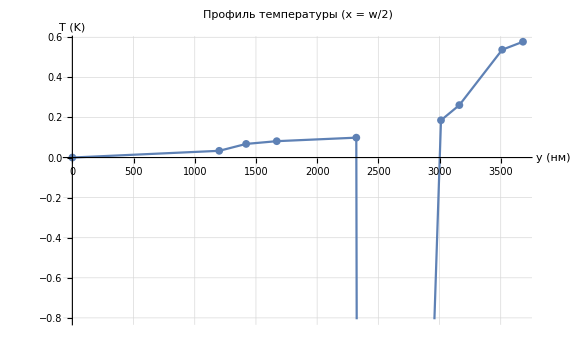

```mathematica
(* ==========ВСПОМОГАТЕЛЬНЫЙ КОД==========*)(*Использует готовое решение sol0 для расчёта температуры*)(*Функция температуры в слое i в точке y*)Tlayer[i_,y_]:=-q[[i]]/(2 k[[i]]) y^2+(A0[i]/.sol0) y+(B0[i]/.sol0)

(*Массивы для удобства*)
q={q1,q2,q3,q4,q5,q6,q7,q8,q9};
k={k1,k2,k3,k4,k5,k6,k7,k8,k9};
yBoundary={0,y1,y2,y3,y4,y5,y6,y7,y8,y9};

(*Вычисляем температуру на каждой границе*)
temperatures=Table[Which[y==0,Tlayer[1,0],y==y1,Tlayer[1,y1],y==y2,Tlayer[2,y2],y==y3,Tlayer[3,y3],y==y4,Tlayer[4,y4],y==y5,Tlayer[5,y5],y==y6,Tlayer[6,y6],y==y7,Tlayer[7,y7],y==y8,Tlayer[8,y8],y==y9,Tlayer[9,y9]],{y,yBoundary}];

(*Вывод в консоль*)
Print["Температура на границах слоёв (x = w/2):"];
Print["y = 0      : T = ",temperatures[[1]]," K"];
Print["y = y1     : T = ",temperatures[[2]]," K"];
Print["y = y2     : T = ",temperatures[[3]]," K"];
Print["y = y3     : T = ",temperatures[[4]]," K"];
Print["y = y4     : T = ",temperatures[[5]]," K"];
Print["y = y5     : T = ",temperatures[[6]]," K"];
Print["y = y6     : T = ",temperatures[[7]]," K"];
Print["y = y7     : T = ",temperatures[[8]]," K"];
Print["y = y8     : T = ",temperatures[[9]]," K"];
Print["y = y9     : T = ",temperatures[[10]]," K"];

(*Построение графика*)
points=Transpose[{yBoundary*10^9,temperatures}];
ListPlot[points,Joined->True,PlotMarkers->{Automatic,8},AxesLabel->{"y (нм)","T (K)"},PlotLabel->"Профиль температуры (x = w/2)",GridLines->Automatic,ImageSize->Large]
```

```mathematica
(* ===ВЫЧИСЛЕНИЕ ТЕМПЕРАТУРЫ НА ГРАНИЦАХ СЛОЁВ===*)(*Задаём x,для которого считаем*)x0=w/2;(*можно заменить на 0,w/2,w*)Print["x = ",x0*10^6," мкм"];

(*Частное решение на границах слоёв*)
Print["\nЧАСТНОЕ РЕШЕНИЕ (n=0):"];
Print["y = 0      : T = ",(B0[1]/.sol0)];
Print["y = y1     : T = ",(-q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))];
Print["y = y2     : T = ",(-q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))];
Print["y = y3     : T = ",(-q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))];
Print["y = y4     : T = ",(-q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))];
Print["y = y5     : T = ",(-q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))];
Print["y = y6     : T = ",(-q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))];
Print["y = y7     : T = ",(-q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))];
Print["y = y8     : T = ",(-q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))];
Print["y = y9     : T = ",(-q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))];

(*Если есть однородные моды—выводим их вклад*)
If[ValueQ[solsN]&&solsN=!={},Print["\nВКЛАД ОДНОРОДНЫХ МОД ПРИ x = ",x0*10^6," мкм:"];
(*Функция для вычисления вклада всех мод в точке (x,y)*)ThPoint[x_,y_]:=Sum[Module[{n=s[[1]],α=(π s[[1]])/w,sol=s[[2]]},((An[1]/.sol) Sinh[α y]+(Bn[1]/.sol) Cosh[α y]) Cos[α x]],{s,solsN}];
Print["y = 0      : Th = ",ThPoint[x0,0]];
Print["y = y1     : Th = ",ThPoint[x0,y1]];
Print["y = y2     : Th = ",ThPoint[x0,y2]];
Print["y = y3     : Th = ",ThPoint[x0,y3]];
Print["y = y4     : Th = ",ThPoint[x0,y4]];
Print["y = y5     : Th = ",ThPoint[x0,y5]];
Print["y = y6     : Th = ",ThPoint[x0,y6]];
Print["y = y7     : Th = ",ThPoint[x0,y7]];
Print["y = y8     : Th = ",ThPoint[x0,y8]];
Print["y = y9     : Th = ",ThPoint[x0,y9]];
Print["\nПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = ",x0*10^6," мкм:"];
Print["y = 0      : T = ",(B0[1]/.sol0)+ThPoint[x0,0]];
Print["y = y1     : T = ",(-q1/(2 k1) y1^2+(A0[1]/.sol0) y1+(B0[1]/.sol0))+ThPoint[x0,y1]];
Print["y = y2     : T = ",(-q2/(2 k2) y2^2+(A0[2]/.sol0) y2+(B0[2]/.sol0))+ThPoint[x0,y2]];
Print["y = y3     : T = ",(-q3/(2 k3) y3^2+(A0[3]/.sol0) y3+(B0[3]/.sol0))+ThPoint[x0,y3]];
Print["y = y4     : T = ",(-q4/(2 k4) y4^2+(A0[4]/.sol0) y4+(B0[4]/.sol0))+ThPoint[x0,y4]];
Print["y = y5     : T = ",(-q5/(2 k5) y5^2+(A0[5]/.sol0) y5+(B0[5]/.sol0))+ThPoint[x0,y5]];
Print["y = y6     : T = ",(-q6/(2 k6) y6^2+(A0[6]/.sol0) y6+(B0[6]/.sol0))+ThPoint[x0,y6]];
Print["y = y7     : T = ",(-q7/(2 k7) y7^2+(A0[7]/.sol0) y7+(B0[7]/.sol0))+ThPoint[x0,y7]];
Print["y = y8     : T = ",(-q8/(2 k8) y8^2+(A0[8]/.sol0) y8+(B0[8]/.sol0))+ThPoint[x0,y8]];
Print["y = y9     : T = ",(-q9/(2 k9) y9^2+(A0[9]/.sol0) y9+(B0[9]/.sol0))+ThPoint[x0,y9]];,Print["\n(Однородные моды не найдены или не заданы.)"]]
```

x = 200 мкм

ЧАСТНОЕ РЕШЕНИЕ (n=0):

y = 0      : T = 0.

y = y1     : T = 0.265942

y = y2     : T = 0.533765

y = y3     : T = 0.837791

y = y4     : T = 0.980196

y = y5     : T = 0.98743

y = y6     : T = 1.06947

y = y7     : T = 1.17273

y = y8     : T = 1.41346

y = y9     : T = 1.43471

ВКЛАД ОДНОРОДНЫХ МОД ПРИ x = 200 мкм:

y = 0      : Th = 378.196

y = y1     : Th = 378.289

y = y2     : Th = 378.327

y = y3     : Th = 378.377

y = y4     : Th = 378.545

y = y5     : Th = 378.558

y = y6     : Th = 378.785

y = y7     : Th = 378.845

y = y8     : Th = 378.997

y = y9     : Th = 379.077

ПОЛНАЯ ТЕМПЕРАТУРА (частное + моды) ПРИ x = 200 мкм:

y = 0      : T = 378.196

y = y1     : T = 378.555

y = y2     : T = 378.86

y = y3     : T = 379.215

y = y4     : T = 379.525

y = y5     : T = 379.545

y = y6     : T = 379.854

y = y7     : T = 380.018

y = y8     : T = 380.411

y = y9     : T = 380.512

```mathematica
(* ==========ФИЗИЧЕСКИЕ ПАРАМЕТРЫ==========*)w=400*10^-6;
L=4*10^-3;

y1=1200*10^-9;y2=1420*10^-9;y3=1670*10^-9;y4=2320*10^-9;
y5=2362*10^-9;y6=3012*10^-9;y7=3162*10^-9;y8=3512*10^-9;y9=3682*10^-9;

k1=55;k2=10;k3=10;k4=55;k5=55;
k6=55;k7=10;k8=10;k9=55;

q1=-2.44*10^10;q2=-5.08*10^9;q3=-9.77*10^10;q4=-3.05*10^11;
q5=-1.18*10^14;
q6=-1.63*10^11;q7=-5.43*10^10;q8=-1.52*10^10;q9=-8.71*10^8;

a=150*10^-6;b=250*10^-6;qr=-5*10^5;
f0=qr (b-a)/w;

(* ==========СИСТЕМА ДЛЯ ЧАСТНОГО РЕШЕНИЯ (n=0)==========*)

vars0={A0[1],B0[1],A0[2],B0[2],A0[3],B0[3],A0[4],B0[4],A0[5],B0[5],A0[6],B0[6],A0[7],B0[7],A0[8],B0[8],A0[9],B0[9]};

(*Нижнее условие:теплоизоляция*)
eq1=B0[1]==0; 

(*Стык 1-2*)
eq2=q1/(2 k1) y1^2+A0[1] y1+B0[1]==q2/(2 k2) y1^2+A0[2] y1+B0[2];
eq3=q1 y1+k1 A0[1]==q2 y1+k2 A0[2];

(*Стык 2-3*)
eq4=q2/(2 k2) y2^2+A0[2] y2+B0[2]==q3/(2 k3) y2^2+A0[3] y2+B0[3];
eq5=q2 y2+k2 A0[2]==q3 y2+k3 A0[3];

(*Стык 3-4*)
eq6=q3/(2 k3) y3^2+A0[3] y3+B0[3]==q4/(2 k4) y3^2+A0[4] y3+B0[4];
eq7=q3 y3+k3 A0[3]==q4 y3+k4 A0[4];

(*Стык 4-5*)
eq8=q4/(2 k4) y4^2+A0[4] y4+B0[4]==q5/(2 k5) y4^2+A0[5] y4+B0[5];
eq9=q4 y4+k4 A0[4]==q5 y4+k5 A0[5];

(*Стык 5-6*)
eq10=q5/(2 k5) y5^2+A0[5] y5+B0[5]==q6/(2 k6) y5^2+A0[6] y5+B0[6];
eq11=q5 y5+k5 A0[5]==q6 y5+k6 A0[6];

(*Стык 6-7*)
eq12=q6/(2 k6) y6^2+A0[6] y6+B0[6]==q7/(2 k7) y6^2+A0[7] y6+B0[7];
eq13=q6 y6+k6 A0[6]==q7 y6+k7 A0[7];

(*Стык 7-8*)
eq14=q7/(2 k7) y7^2+A0[7] y7+B0[7]==q8/(2 k8) y7^2+A0[8] y7+B0[8];
eq15=q7 y7+k7 A0[7]==q8 y7+k8 A0[8];

(*Стык 8-9*)
eq16=q8/(2 k8) y8^2+A0[8] y8+B0[8]==q9/(2 k9) y8^2+A0[9] y8+B0[9];
eq17=q8 y8+k8 A0[8]==q9 y8+k9 A0[9];

(*Верхнее условие:поток от провода (без лишнего минуса)*)
eq18=q9/k9 y9+A0[9]==f0;

system0={eq1,eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9,eq10,eq11,eq12,eq13,eq14,eq15,eq16,eq17,eq18};

sol0=NSolve[system0,vars0][[1]]
```

{A0[1]→-28115.7,B0[1]→0.,A0[2]→-156955.,B0[2]→0.154653,A0[3]→-143803.,B0[3]→0.145315,A0[4]→-19851.6,B0[4]→-0.0675741,A0[5]→4.94474×10^6,B0[5]→-5.8265,A0[6]→-115826.,B0[6]→0.150028,A0[7]→-669784.,B0[7]→1.82974,A0[8]→-682147.,B0[8]→1.84928,A0[9]→-124942.,B0[9]→-0.116899}